# Simulation on SMWDC ray - tracking

assume there are 6 planes XX' UU' VV’
each cells with size 20 mm X 16 mm
O’ planes are shifted by 5mm
a particle pass throught the MWDC and created signal
	signal constains : 
 	1) # of wire hitted
 	2) hitted wire ID
 	3) the Leading edge of the signal
 by using the drift velocity, we can reconstruct the particle ray.
 the origin of the cooredinate is

```mathematica
(* have to rotate the UU' and VV' plan *)
```

```mathematica
(* initial *)
a=1;
Clear[a];
```

k is alway {x, a , y, b}
Ray is a 3D lines

## Raw Signal Generation

```mathematica
(* a paricle's travaling path *)
(* k = {x0, a, y0, b} *)
(* 3D Ray *)
Ray[k_,z_]:={k[[1]]+k[[2]]z,k[[3]]+k[[4]]z,z}
(* the {x,y} @ z=-40, z=40 *)
Bound[k_]:={Ray[k,-40][[1;;2]],Ray[k,40][[1;;2]]}
(* Normal of Ray *)
NormRay[k_]:=Normalize[(Ray[k,40]-Ray[k,-40])]
```

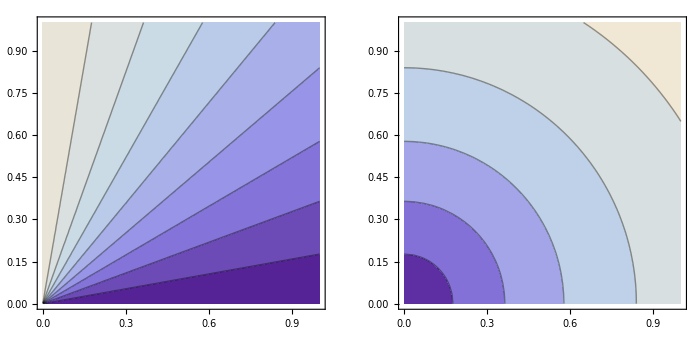

```mathematica
GraphicsGrid[{{
ContourPlot[ArcTan[y/x] 180/π,{x,0.0001,1},{y,0.0001,1}] ,
ContourPlot[ArcTan[√(x^2+y^2)] 180/π,{x,0.0001,1},{y,0.0001,1}]}},ImageSize->700]
```

## MWDC Construction

```mathematica
(* plan angle *)
planθ[plan_]:=Switch[plan,
1,0,
2,0,
3,ArcCos[0.8],
4,ArcCos[0.8],
5,-ArcCos[0.8],
6,-ArcCos[0.8]
]
(* wire direction *)
wnorm[plan_]:={-Sin[planθ[plan]],Cos[planθ[plan]],0}
cell(*X,Y,Z*)={20,400,16};
firstwirePosition(*mm*)={0,5,13.125,9.5,13.125,9.5};
wstart[plan_,i_]:=
{(i-1)cell[[1]]/Cos[planθ[plan]]+firstwirePosition[[plan]],0,cell[[3]](plan-1)-40}
(* wire *)
w[plan_,i_,s_]:=wstart[plan,i]+s wnorm[plan]
(* number of wire *)
numWire[plan_]:=Switch[plan,
1,56,
2,56,
3,44,
4,44,
5,44,
6,44
]
(* Hightlight wire cell *)
Highlight[plane_,wire_,lis_]:=If[MemberQ[lis,{plane,wire,__}],0.5,0.1]
```

### chamber geometery drawing: MWDC[k,XYZ,size,α] MWDC2[k,size, α]

```mathematica
MWDC[k_,XYZ_, size_, α_]:=Module[{J},Graphics3D[{
J=HitList[k];
{Black,Arrow[{{0,0,-40},{0,0,100}}]},
{Black,Arrow[{{0,0,-40},{1120,0,-40}}]},
{Black,Arrow[{{0,0,-40},{0,250,-40}}]},
{Red,Arrow[{Ray[k,-70],Ray[k,70]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,1,numWire[1]}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,1,numWire[2]}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planθ[3]],1}],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,1,numWire[3]}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planθ[4]],1}],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,1,numWire[4]}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planθ[5]],1}],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,1,numWire[5]}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planθ[6]],1}],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,1,numWire[6]}]
}, ImageSize->size, PlotRange->XYZ]]
MWDC2[k_, size_, α_]:=Graphics3D[{
J=HitList[k];
fp=FirstPlan[J];
Ymin=Min[Ray[k,-60][[2]],Ray[k,60][[2]]]-20;
Ymax=Max[Ray[k,-60][[2]],Ray[k,60][[2]]]+20;
Corner1[plan_]:={-cell[[1]]/2,Ymin/Cos[planθ[plan]],-cell[[3]]/2};
Corner2[plan_]:={cell[[1]]/2,Ymax/Cos[planθ[plan]],cell[[3]]/2};
(*Z*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,Ray[k,60][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Ray[k,-60],Ray[k,60]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J[[1,2]]-2,J[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J[[fp[[2]],2]]-2,J[[fp[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-2,J[[fp[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-2,J[[fp[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-2,J[[fp[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-2,J[[fp[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J[[i,1]],J[[i,2]],(Ymin-20)/Cos[planθ[J[[i,1]]]]],w[J[[i,1]],J[[i,2]],(Ymax+20)/Cos[planθ[J[[i,1]]]]]},J[[i,5]]]},{i,1,Length[J]}],
Text[J[[1,2]],w[J[[1,1]],J[[1,2]],0]+{-10,0,0}]
}, ImageSize->size]
```

```mathematica
MWDC[Rayk[1,60,0],{{20*38,20*57},{-200,200},{-50,50}},500,0.2]
```

-Graphics3D-

```mathematica
k={552.5,0,0,0};
MWDC2[k,500,0.5]
J//TableForm
```

-Graphics3D-

1 | 29 | -40 | 0. | 7.5 | 560
2 | 28 | -24 | 0. | 7.5 | 545
3 | 23 | -8 | 6.375 | 8.5 | 450.5
4 | 23 | 8 | 4.2 | 5.6 | 447.6
5 | 23 | 24 | -6.375 | 8.5 | 450.5
6 | 23 | 40 | -4.2 | 5.6 | 447.6

### MWDC full drawing

```mathematica
MWDCfull[k_, size_, α_]:=Module[{J},Graphics3D[{
J=HitList[k];
{Black,Arrow[{{0,0,-40},{0,0,100}}]},
{Black,Arrow[{{0,0,-40},{1120,0,-40}}]},
{Black,Arrow[{{0,0,-40},{0,250,-40}}]},
{Blue,
Arrow[{Crystal[1],Crystal[1]+600{-√3,0,1}}],
Arrow[{Crystal[1],Crystal[1]+{0,200,0}}],
Arrow[{Crystal[1],Crystal[1]+200{1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[1][[3]]],Ray[k,70]}]},
{Blue,
Arrow[{Crystal[2],Crystal[2]+600{√3,0,1}}],
Arrow[{Crystal[2],Crystal[2]+{0,200,0}}],
Arrow[{Crystal[2],Crystal[2]+200{-1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[2][[3]]],Ray[k,70]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,1,numWire[1]}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,1,numWire[2]}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planθ[3]],1}],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,1,numWire[3]}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planθ[4]],1}],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,1,numWire[4]}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planθ[5]],1}],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,1,numWire[5]}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planθ[6]],1}],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,1,numWire[6]}]
}, ImageSize->size, PlotRange->All]]
```

```mathematica
MWDCfull[Rayk[1,50,-9],1000,0.1]
```

-Graphics3D-

```mathematica
MWDCfull2[k_, size_, α_]:=Module[{J,fp},Graphics3D[{
J=HitList[k];
fp=LastPlan[J];
{Black,Arrow[{{0,0,0},{0,0,60}}]},
{Black,Arrow[{{0,0,0},{1120,0,0}}]},
{Black,Arrow[{{0,0,0},{0,250,0}}]},
{Blue,
Arrow[{Crystal[1],Crystal[1]+600{-√3,0,1}}],
Arrow[{Crystal[1],Crystal[1]+{0,200,0}}],
Arrow[{Crystal[1],Crystal[1]+200{1,0,√3}}]},
{Red,Arrow[{Ray[k,Crystal[1][[3]]],Ray[k,70]}]},
{Blue,
Arrow[{Crystal[2],Crystal[2]+600{√3,0,1}}],
Arrow[{Crystal[2],Crystal[2]+{0,200,0}}],
Arrow[{Crystal[2],Crystal[2]+200{-1,0,√3}}]},
(*{Red,Arrow[{Ray[k,Crystal[2][[3]]],Ray[k,70]}]},*)
Text[J,{500,0,-400}],
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+1/2 cell,wstart[1,i]-1/2 cell]},{i,J[[fp[[1]],2]]-1,J[[fp[[1]],2]]+1}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+1/2 cell,wstart[2,i]-1/2 cell]},{i,J[[fp[[2]],2]]-1,J[[fp[[2]],2]]+1}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+1/2 cell{1,1/Cos[planθ[3]],1},wstart[3,i]-1/2 cell{1,1/Cos[planθ[3]],1}],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-1,J[[fp[[3]],2]]+1}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+1/2 cell{1,1/Cos[planθ[4]],1},wstart[4,i]-1/2 cell{1,1/Cos[planθ[4]],1}],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-1,J[[fp[[4]],2]]+1}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+1/2 cell{1,1/Cos[planθ[5]],1},wstart[5,i]-1/2 cell{1,1/Cos[planθ[5]],1}],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-1,J[[fp[[5]],2]]+1}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+1/2 cell{1,1/Cos[planθ[6]],1},wstart[6,i]-1/2 cell{1,1/Cos[planθ[6]],1}],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-1,J[[fp[[6]],2]]+1}]
}, ImageSize->size, PlotRange->All]]
```

```mathematica
Manipulate[MWDCfull2[Rayk[mwdc,θ,ϕ],700,0.1],{{θ,60},20,70},{{ϕ,0},-15,15},{mwdc,{1,2}}]
```

### MWDC2Rays drawing : MWDC2Rays[k1,k2,size,α], MWDC2RaysFlat[k1,k2,size,α,start plane]

```mathematica
MWDC2Rays[k1_, k2_,size_, α_]:=Graphics3D[{
J1=HitList[k1];
fp1=FirstPlan[J1];
J2=HitList[k2];
fp2=FirstPlan[J2];
Ymin=Min[Ray[k1,-60][[2]],Ray[k1,60][[2]],Ray[k2,60][[2]],Ray[k2,60][[2]]]-20;
Ymax=Max[Ray[k1,-60][[2]],Ray[k1,60][[2]],Ray[k2,60][[2]],Ray[k2,60][[2]]]+20;
Corner1[plan_]:={-cell[[1]]/2,Ymin/Cos[planθ[plan]],-cell[[3]]/2};
Corner2[plan_]:={cell[[1]]/2,Ymax/Cos[planθ[plan]],cell[[3]]/2};
(*Z*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J1[[1,1]],J1[[1,2]],0],w[J1[[1,1]],J1[[1,2]],0]+{0,Ray[k1,60][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Ray[k1,-60],Ray[k1,60]}]},
{Orange,Thickness[Large ],Arrow[{Ray[k2,-60],Ray[k2,60]}]},
Table[{Green,Opacity[Highlight[1,i,J1]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J1[[1,2]]-2,J1[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J1]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J1[[fp1[[2]],2]]-2,J1[[fp1[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,J1[[fp1[[3]],2]]-2,J1[[fp1[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,J1[[fp1[[4]],2]]-2,J1[[fp1[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,J1[[fp1[[5]],2]]-2,J1[[fp1[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J1]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,J1[[fp1[[6]],2]]-2,J1[[fp1[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J1[[i,1]],J1[[i,2]],Ymin-20],w[J1[[i,1]],J1[[i,2]],Ymax+20]},J1[[i,5]]]},{i,1,Length[J1]}],
Table[{Cyan,Opacity[0.5],Cylinder[{w[J2[[i,1]],J2[[i,2]],Ymin-20],w[J2[[i,1]],J2[[i,2]],Ymax+20]},J2[[i,5]]]},{i,1,Length[J2]}]
}, ImageSize->size]
MWDC2RaysFlat[k1_,k2_, size_, α_,plan_]:=(*ImageReflect[*)Graphics[{
J1=HitList[k1];
J2=HitList[k2];
fp1=FirstPlan[J1];
fp2=FirstPlan[J2];
(*Z*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{0,30}}]},
(*X*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{30,0}}]},
{Red,Thickness[Large ],Arrow[{Drop[Ray[k1,-50],{2}],Drop[Ray[k1,-10],{2}]}]},
{Blue,Thickness[Large ],Arrow[{Drop[Ray[k2,-50],{2}],Drop[Ray[k2,-10],{2}]}]},
Table[{Green,Opacity[0.2],EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan,i]-1/2 cell/{wnorm[plan][[2]],1,1},{2}],Drop[wstart[plan,i]+1/2 cell/{wnorm[plan][[2]],1,1},{2}]]},{i,J1[[fp1[[plan]],2]],J1[[fp1[[plan]],2]]+2}],
Table[{Green,Opacity[0.2],,EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan+1,i]-1/2 cell/{wnorm[plan+1][[2]],1,1},{2}],Drop[wstart[plan+1,i]+1/2 cell/{wnorm[plan+1][[2]],1,1},{2}]]},{i,J1[[fp1[[plan+1]],2]],J1[[fp1[[plan+1]],2]]+2}],
Table[{Red,
Circle[Drop[w[J1[[i,1]],J1[[i,2]],0],{2}],{J1[[i,5]]/(wnorm[plan][[2]]),J1[[i,5]]}]},{i,fp1[[plan]],fp1[[plan+1]]+1}],
Table[{Blue,
Circle[Drop[w[J2[[i,1]],J2[[i,2]],0],{2}],{J2[[i,5]]/(wnorm[plan][[2]]),J2[[i,5]]}]},{i,fp2[[plan]],fp2[[plan+1]]+1}],
Text[{J1[[1,2]],J1[[1,6]]-Crystal[1][[1]]},Drop[w[J1[[1,1]],J1[[1,2]],0]+{-5,0,0},{2}]],
Text[{J1[[fp1[[2]],2]],J1[[fp1[[2]],6]]-Crystal[1][[1]]},Drop[w[J1[[fp1[[2]],1]],J1[[fp1[[2]],2]],0]+{-5,0,0},{2}]]
}, ImageSize->size](*,Left->Right]*)
```

```mathematica
MWDC2Rays[Rayk[1,41,0],Rayk[1,42,4],500,0.1]
```

-Graphics3D-

```mathematica
fp1
J1//TableForm
```

{1,3,4,5,6,7}

1 | 10 | -40 | 0. | 8.26529 | 180 | 10.5759
1 | 11 | -40 | 0. | 7.36512 | 200 | 9.42409
2 | 10 | -24 | 0. | 5.62438 | 185 | 7.19672
3 | 7 | -8 | -0.812152 | 1.28486 | 130.5 | 1.52452
4 | 7 | 8 | 3.0864 | 4.8828 | 127.6 | 5.79359
5 | 6 | 24 | 0.579771 | 0.917219 | 110.5 | 1.08831
6 | 6 | 40 | -3.31878 | 5.25044 | 107.6 | 6.2298

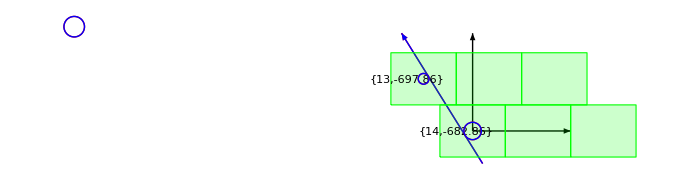

1 | 14 | -40 | -122.873 | 2.66869 | 260 | 3.14
2 | 13 | -24 | -124.518 | 1.64881 | 245 | 1.94
3 | 6 | -8 | -159.586 | 3.14386 | 110.5 | 3.588
4 | 6 | 8 | -157.709 | 2.02581 | 107.6 | 2.312
5 | 13 | 24 | -160.657 | 0.45732 | 250.5 | 0.5
6 | 13 | 40 | -164.901 | 3.35856 | 247.6 | 3.672

-Graphics3D-

```mathematica
k={-710.8,-0.62,-126.6,-0.09}+{Crystal[1][[1]],0,0,0};
MWDC2RaysFlat[k,k,700,1,1]
ShortedHitList[k]//TableForm
MWDC2[k,500,0.1]
```

## Signal Construction

```mathematica
(* a shortest distance between 2 lines*) 
MaxDriftLen[plan_]:=Switch[plan,
1,12,
2,12,
3,12,
4,12,
5,12,
6,12
]
DriftLen[k_,plan_,i_]:={s,z,dl}/.Flatten[Solve[w[plan,i,s]+dl Normalize[Cross[wnorm[plan],NormRay[k]]]==Ray[k,z],{s,z,dl}]]
(* another method to calculate driftlenght *)
DriftLength[k_,plan_,i_]:=Abs[(wstart[plan,i]-Ray[k,0]).Normalize[Cross[wnorm[plan],NormRay[k]]]]
(* general 2 ray distance *)
Distance[ray1_,ray1Norm_,ray2_,ray2Norm_]:=Abs[(ray1-ray2).Normalize[Cross[ray1Norm,ray2Norm]]]
HitList[k_]:= (* plane, wire, z, s, DL, wire Distance *)
Flatten[DeleteCases[Table[If[Abs[DriftLen[k,plan,i][[3]]]<MaxDriftLen[plan],
{plan,i,(plan-1)*cell[[3]]-40,DriftLen[k,plan,i][[1]],Abs[DriftLen[k,plan,i][[3]]],Distance[wstart[plan,i],wnorm[plan],{0,0,0},{0,0,1}],Abs[(DriftLen[k,plan,i][[3]])/Cos[IncAng[k][[plan]]]]},0]
,{plan,1,6},{i,1,numWire[plan]}]
,0,2]
,1]
CountPlan[Lis_]:=Table[Count[Transpose[Lis][[1]],i],{i,1,6}];
FirstPlan[Lis_]:=Flatten[Table[Position[Lis,{i,__}][[1]],{i,1,6}]];
(* If plan does not exit, use last plan *)
LastPlan[Lis_]:=Table[Total[CountPlan[Lis][[1;;i]]],{i,1,6}];
ReducedFstHitList[k_]:=Module[{J,FstPlan},J=HitList[k];FstPlan=LastPlan[J];Table[J[[i]],{i,FstPlan}]]
ShortedHitList[k_]:=Module[{J,multi,FstPlan},J=HitList[k];multi=CountPlan[J];FstPlan=LastPlan[J];
DeleteCases[Table[If[multi[[i]]==0,0,If[multi[[i]]≠1 ,
If[ J[[FstPlan[[i]],5]]<J[[FstPlan[[i]]-1,5]],J[[FstPlan[[i]]]],J[[FstPlan[[i]]-1]]],
J[[FstPlan[[i]]]]
]],{i,6}],0,1]
]
```

```mathematica
k=Rayk[1,20,-5];
J=HitList[k];
J//TableForm
CountPlan[J]
LastPlan[J]
ShortedHitList[k]//TableForm
```

1 | 8 | -40 | -36.9193 | 7.76797 | 140 | 10.1508
1 | 9 | -40 | -36.5353 | 7.53718 | 160 | 9.84921
2 | 7 | -24 | -37.5724 | 8.94724 | 125 | 11.6918
2 | 8 | -24 | -37.1884 | 6.35791 | 145 | 8.3082
3 | 4 | -8 | -50.2642 | 4.35219 | 70.5 | 5.30339
4 | 4 | 8 | -46.6927 | 2.41099 | 67.6 | 2.93792
5 | 5 | 24 | -43.9292 | 8.45567 | 90.5 | 10.083
5 | 6 | 24 | -54.0332 | 8.31652 | 110.5 | 9.91704
6 | 5 | 40 | -48.4941 | 2.1719 | 87.6 | 2.58989

{2,2,1,1,2,1}

{2,4,5,6,8,9}

1 | 9 | -40 | -36.5353 | 7.53718 | 160 | 9.84921
2 | 8 | -24 | -37.1884 | 6.35791 | 145 | 8.3082
3 | 4 | -8 | -50.2642 | 4.35219 | 70.5 | 5.30339
4 | 4 | 8 | -46.6927 | 2.41099 | 67.6 | 2.93792
5 | 6 | 24 | -54.0332 | 8.31652 | 110.5 | 9.91704
6 | 5 | 40 | -48.4941 | 2.1719 | 87.6 | 2.58989

## Drift-Time to Drift-Length Conversion

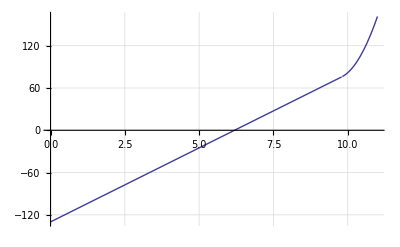

```mathematica
DLcDT[dl_]:=Module[{cut},cut=9.8;Piecewise[{{dl/2,dl<cut},{dl^2+(1/2-2 cut)dl+(cut)^2,dl≥  cut}}] 210/5-130]
Plot[DLcDT[x],{x,0,11},GridLines->Automatic]
```

```mathematica
InverseFunction[DLcDT][50]
```

8.57143

### Drift Time - Drift Length

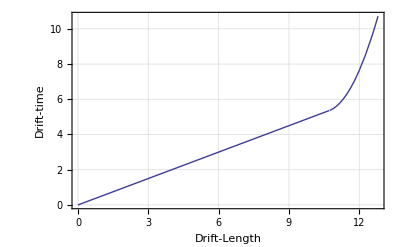

```mathematica
DriftTime[x_]:=Piecewise[{{x/2,x<10.7212},{x^2+(1/2-2 10.7212)x+(10.7212)^2,x≥  10.7212}}]
Plot[DriftTime[x],{x,0,12.8}, Frame->True, FrameLabel->{"Drift-Length","Drift-time"}, GridLines->Automatic]
```

## Target Geometry

```mathematica
Crystal[mwdc_]:=Switch[mwdc,
(*1,{942.86,0,-1400}, Plastics*)
1,{390.36+552.5,0,-982.37},
2,{-390.36+552.5,0,-982.37}
]
(* norm Ray vector in mwdc frame, {θ,ϕ} = lab angle *)
Rayn[mwdc_,θ_,ϕ_]:=RotationMatrix[(-1)^mwdc π/3,{0,1,0}].{(-1)^(mwdc+1)Sin[θ °]Cos[ϕ °],(-1)^(mwdc+1)Sin[θ °]Sin[ϕ °],Cos[θ °]}
(* Ray from Crystal *)
RayC[mwdc_,θ_,ϕ_,s_]:=Crystal[mwdc]+s Rayn[mwdc,θ,ϕ]
Rayk[mwdc_,θ_,ϕ_]:={
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[1]],
Map[(#1[[1]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]],
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[2]],
Map[(#1[[2]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]]} 
LabAngleShift[mwdc_]:=Switch[mwdc,
1,-30,
2,150
]
LabAngle [mwdc_,plan_,wire_](*right-low corner, wire, left-up corner*):={LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire]+{-10,0,-8})+Crystal[mwdc])].{1,0,0}]*180/π, (* corner *)
LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire])+Crystal[mwdc])].{1,0,0}]*180/π, (* wire *)LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[plan,wire]+{10,0,8})+Crystal[mwdc])].{1,0,0}]*180/π} (* corner *)
```

```mathematica
PolarAngle[ray_]:=If[ray[[2]]==0 && ray[[1]]==0, {0,0},{ArcTan[ray[[3]],Norm[ray[[1;;2]]]],ArcTan[ray[[1]],ray[[2]]]}]
XY2angle[mwdc_,k_]:=PolarAngle[RotationMatrix[-(-1)^mwdc π/3,{0,1,0}].Normalize[{k[[1]]-Crystal[mwdc][[1]],k[[3]],-Crystal[mwdc][[3]]}]]
```

```mathematica
IncAng[k_]:=Module[{normk,pk},
normk=NormRay[k];
Table[
(*pk=Normalize[normk-(normk.wnorm[i])wnorm[i]];*)
pk=normk[[3]]/(√(1-(normk.wnorm[i])^2));
ArcCos[pk]
,{i,1,6}]
]
```

```mathematica
IncAngX=Monitor[Table[{θ,ϕ,IncAng[Rayk[1,θ,ϕ]][[1]] 180/π},{θ,20,70,1},{ϕ,-10,10,1}],{θ,ϕ}];
IncAngU=Monitor[Table[{θ,ϕ,IncAng[Rayk[1,θ,ϕ]][[3]] 180/π},{θ,20,70,1},{ϕ,-10,10,1}],{θ,ϕ}];
IncAngV=Monitor[Table[{θ,ϕ,IncAng[Rayk[1,θ,ϕ]][[5]] 180/π},{θ,20,70,1},{ϕ,-10,10,1}],{θ,ϕ}];
```

```mathematica
ListPlot3D[{Flatten[IncAngX,1],Flatten[IncAngU,1],Flatten[IncAngV,1]},PlotStyle->{Green,Yellow,Blue}]
```

-Graphics3D-

## ReConstruction - Multi - Demension Regession

### General

```mathematica
h[z1_,z2_,z3_,z4_,z5_,z6_]:={
{Cos[planθ[1]],Cos[planθ[1]]z1,Sin[planθ[1]],Sin[planθ[1]]z1},
{Cos[planθ[2]],Cos[planθ[2]]z2,Sin[planθ[2]],Sin[planθ[2]]z2},
{Cos[planθ[3]] ,Cos[planθ[3]] z3,Sin[planθ[3]],Sin[planθ[3]]z3},
{ Cos[planθ[4]],Cos[planθ[4]] z4,Sin[planθ[4]],Sin[planθ[4]]z4},
{Cos[planθ[5]],Cos[planθ[5]] z5,Sin[planθ[5]],Sin[planθ[5]]z5},
{Cos[planθ[6]], Cos[planθ[6]]z6,Sin[planθ[6]],Sin[planθ[6]]z6}
}
h6=h[-40,-24,-8,8,24,40];
M6=Inverse[Transpose[h6].h6].Transpose[h6];
P6=h6.M6;
zpos[plane_]:=Switch[plane,
1,-40,
2,-24,
3,-8,
4,8,
5,24,
6,40]
hG[planeID_]:=Table[
{Cos[planθ[planeID[[i]]]],Cos[planθ[planeID[[i]]]]zpos[planeID[[i]]],Sin[planθ[planeID[[i]]]],Sin[planθ[planeID[[i]]]]zpos[planeID[[i]]]}
,{i,1,Length[planeID]}]
MG[planeID_]:=Inverse[Transpose[hG[planeID]].hG[planeID]].Transpose[hG[planeID]]
(* Hit List Function *)
Binery[n_,digit_]:=If[Length[IntegerDigits[n,2]]<digit, 
Join[ Reverse[IntegerDigits[n,2]],Table[0,{i,1,digit-Length[IntegerDigits[n,2]]}]],
Reverse[IntegerDigits[n,2]]]
InputDist[J_]:=Module[{plan,wiredist, dist},
Table[plan=LastPlan[J][[i]];
wiredist=Transpose[J][[6,plan]];
(* Projection of the drift-length on the wire plane *)
dist=Transpose[J][[5,plan]] (*(√((Crystal[1][[1]]-wiredist)^2+(Abs[Crystal[1][[3]]-J[[plan,3]]])^2))/Abs[Crystal[1][[3]]-J[[plan,3]]]*);
{wiredist-dist,
wiredist+dist}
,{i,1,Length[plan]}]
]
PossPos[J_,σ_,corr_]:=Module[{len,tran,bin},len=Length[J];tran=Transpose[J];
Table[bin=(-1)^Binery[i,len];tran[[6]]+bin (tran[[If[corr==1,7,5]]]+RandomVariate[NormalDistribution[0,σ],len]),{i,0,2^len-1}]
]
```

```mathematica
(*k=Rayk[1,20];*)
k=Rayk[1,20,0];
MWDC2[k,600,0.1]
HitList[k]//TableForm
J=ShortedHitList[k];
J//TableForm
PosiYList=PossPos[J,0.001,0];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ParameterConfidenceIntervalTable"]
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATable"]
Estβ=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors"}]
PosiYList=PossPos[J,0.001,1];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ParameterConfidenceIntervalTable"]
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATable"]
EstβCorr=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors"}]
{k,
Estβ[[1]],
EstβCorr[[1]],
k-Estβ[[1]],
k-EstβCorr[[1]]}//TableForm
```

-Graphics3D-

1 | 8 | -40 | 0. | 9.28268 | 140 | 12.1177
1 | 9 | -40 | 0. | 6.03821 | 160 | 7.88232
2 | 8 | -24 | 0. | 4.83214 | 145 | 6.30791
3 | 5 | -8 | -5.02193 | 8.06465 | 90.5 | 9.71319
3 | 6 | -8 | 5.3185 | 8.54091 | 110.5 | 10.2868
4 | 5 | 8 | -0.968236 | 1.55488 | 87.6 | 1.87272
5 | 4 | 24 | 4.25625 | 6.83505 | 70.5 | 8.23224
5 | 5 | 24 | -6.08418 | 9.77051 | 90.5 | 11.7678
6 | 4 | 40 | 0.202553 | 0.325277 | 67.6 | 0.391768

1 | 9 | -40 | 0. | 6.03821 | 160 | 7.88232
2 | 8 | -24 | 0. | 4.83214 | 145 | 6.30791
3 | 5 | -8 | -5.02193 | 8.06465 | 90.5 | 9.71319
4 | 5 | 8 | -0.968236 | 1.55488 | 87.6 | 1.87272
5 | 4 | 24 | 4.25625 | 6.83505 | 70.5 | 8.23224
6 | 4 | 40 | 0.202553 | 0.325277 | 67.6 | 0.391768

| Estimate | Standard Error | Confidence Interval
x0 | 117.002 | 0.755417 | {113.751,120.252}
a | -0.933734 | 0.0240862 | {-1.03737,-0.830099}
y0 | -1.96769 | 1.19802 | {-7.12236,3.18699}
b | -0.0803511 | 0.0811128 | {-0.429351,0.268649}

| DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 68161.4 | 68161.4 | 95439.2 | 0.0000104777
a | 1 | 2804.12 | 2804.12 | 3926.32 | 0.000254594
y0 | 1 | 9.64958 | 9.64958 | 13.5113 | 0.0666932
b | 1 | 0.700838 | 0.700838 | 0.981309 | 0.426281
Error | 2 | 1.42837 | 0.714187 |  | 
Total | 6 | 70977.3 |  |  |

{{117.002,-0.933734,-1.96769,-0.0803511},{0.755417,0.0240862,1.19802,0.0811128}}

| Estimate | Standard Error | Confidence Interval
x0 | 118.555 | 0.000726775 | {118.552,118.558}
a | -0.839085 | 0.0000231729 | {-0.839185,-0.838986}
y0 | -0.00031016 | 0.0011526 | {-0.00526939,0.00464907}
b | 0.0000797964 | 0.0000780373 | {-0.000255971,0.000415564}

| DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 68757. | 68757. | 1.04011×10^11 | 9.61442×10^-12
a | 1 | 2488.4 | 2488.4 | 3.76429×10^9 | 2.65654×10^-10
y0 | 1 | 4.0025×10^-7 | 4.0025×10^-7 | 0.605472 | 0.517937
b | 1 | 6.91187×10^-7 | 6.91187×10^-7 | 1.04558 | 0.414073
Error | 2 | 1.32211×10^-6 | 6.61055×10^-7 |  | 
Total | 6 | 71245.4 |  |  |

{{118.555,-0.839085,-0.00031016,0.0000797964},{0.000726775,0.0000231729,0.0011526,0.0000780373}}

118.554 | -0.8391 | 0. | 0.
117.002 | -0.933734 | -1.96769 | -0.0803511
118.555 | -0.839085 | -0.00031016 | 0.0000797964
1.55213 | 0.0946339 | 1.96769 | 0.0803511
-0.00096382 | -0.0000143155 | 0.00031016 | -0.0000797964

```mathematica
(* Correction based on 1st estimation *)
```

```mathematica
IncAng[Estβ[[1]]]
```

{0.751143,0.751143,0.671806,0.671806,0.609904,0.609904}

```mathematica
J//TableForm
```

1 | 9 | -40 | 0. | 6.03821 | 160 | 7.88232
2 | 8 | -24 | 0. | 4.83214 | 145 | 6.30791
3 | 5 | -8 | -5.02193 | 8.06465 | 90.5 | 9.71319
4 | 5 | 8 | -0.968236 | 1.55488 | 87.6 | 1.87272
5 | 4 | 24 | 4.25625 | 6.83505 | 70.5 | 8.23224
6 | 4 | 40 | 0.202553 | 0.325277 | 67.6 | 0.391768

```mathematica
Table[J[[i,7]]=J[[i,5]]/Cos[IncAng[Estβ[[1]]][[i]]],{i,1,6}];
J//TableForm
```

1 | 9 | -40 | 0. | 6.03821 | 160 | 8.26123
2 | 8 | -24 | 0. | 4.83214 | 145 | 6.61114
3 | 5 | -8 | -5.02193 | 8.06465 | 90.5 | 10.3036
4 | 5 | 8 | -0.968236 | 1.55488 | 87.6 | 1.98656
5 | 4 | 24 | 4.25625 | 6.83505 | 70.5 | 8.33845
6 | 4 | 40 | 0.202553 | 0.325277 | 67.6 | 0.396822

```mathematica
PosiYList=PossPos[J,0.001,1];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
EstβCorr2=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors"}]
```

{{118.359,-0.835863,0.801896,-0.0304207},{0.224115,0.00714582,0.355425,0.0240643}}

```mathematica
{k,
Estβ[[1]],
EstβCorr[[1]],
EstβCorr2[[1]],
k-Estβ[[1]],
k-EstβCorr[[1]],
k-EstβCorr2[[1]]}//TableForm
```

118.554 | -0.8391 | 0. | 0.
117.002 | -0.933734 | -1.96769 | -0.0803511
118.555 | -0.839085 | -0.00031016 | 0.0000797964
118.359 | -0.835863 | 0.801896 | -0.0304207
1.55213 | 0.0946339 | 1.96769 | 0.0803511
-0.00096382 | -0.0000143155 | 0.00031016 | -0.0000797964
0.194346 | -0.00323674 | -0.801896 | 0.0304207

```mathematica
Table[J[[i,7]]=J[[i,5]]/Cos[IncAng[Estβ[[1]]][[i]]],{i,1,6}];
PosiYList=PossPos[J,0.001,1];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
EstβCorr3=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors"}]
{k,
Estβ[[1]],
EstβCorr[[1]],
EstβCorr2[[1]],
EstβCorr3[[1]],
k-Estβ[[1]],
k-EstβCorr[[1]],
k-EstβCorr2[[1]],
k-EstβCorr3[[1]]}//TableForm
```

{{118.357,-0.835896,0.803261,-0.0304953},{0.224732,0.0071655,0.356405,0.0241306}}

118.554 | -0.8391 | 0. | 0.
117.002 | -0.933734 | -1.96769 | -0.0803511
118.555 | -0.839085 | -0.00031016 | 0.0000797964
118.359 | -0.835863 | 0.801896 | -0.0304207
118.357 | -0.835896 | 0.803261 | -0.0304953
1.55213 | 0.0946339 | 1.96769 | 0.0803511
-0.00096382 | -0.0000143155 | 0.00031016 | -0.0000797964
0.194346 | -0.00323674 | -0.801896 | 0.0304207
0.196458 | -0.0032039 | -0.803261 | 0.0304953

### Example for MWDC-L

```mathematica
GenPossRay[set_]:=Table[
wstart[set[[j,1]],set[[j,2]]][[1]] wnorm[set[[j,1]]][[2]]+Power[-1,Binery[i,Length[set]][[j]]]set[[j,4]]
,{i,0,2^Length[set]-1},{j,1,Length[set]}]
Convert[lis_,mwdc_,planeID_]:=Table[lis[[i]]-Crystal[mwdc][[1]]Table[Cos[planθ[planeID[[k]]]],{k,1,Length[planeID]}],{i,1,Length[lis]}]
Raw2DL[listraw_]:=Module[{pos,sorted},
sorted=
Table[
pos=Flatten[Position[listraw,{_,i,__}]];
Sort[listraw[[pos]],#1[[4]]<#2[[4]]&][[1]]
,{i,1,6}];
Table[{sorted[[i,2]],sorted[[i,3]],sorted[[i,1]],InverseFunction[DLcDT][sorted[[i,4]]]},{i,1,6}]
]
```

```mathematica
set={
{1,16,0,6.47},
{2,16,0,5.78},
{3,12,0,1.28},
{4,12,0,4.00},
{5,14,0,6.82},
{6,14,0,0.48}};
```

```mathematica
Rayset=GenPossRay[set];
planeID=Table[set[[i,1]],{i,1,Length[set]}];
hh=hG[planeID];
SSError=Table[{i,LinearModelFit[{hh,Rayset[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,Power[2,Length[set]]}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ParameterConfidenceIntervalTable"]
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATable"]
Estk=LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"];
Estk{1,180/π,1,180/π}
Estk+{-Crystal[1][[1]],0,0,0}
J=HitList[Estk];
fp=LastPlan[J]
Table[{J[[fp[[i]],1]],J[[fp[[i]],2]],J[[fp[[i]],-1]],"|",set[[i,1]],set[[i,2]],set[[i,-1]],"|",Abs[set[[i,-1]]-J[[fp[[i]],-1]]]},{i,1,Length[set]}]//TableForm
LabAngle[1,set[[1,1]],set[[1,2]]]
MWDC2[Estk,700,0.1]
```

| Estimate | Standard Error | Confidence Interval
x0 | 160.399 | 0.0584653 | {160.147,160.651}
a | -1.04946 | 0.00186414 | {-1.05748,-1.04144}
y0 | -154.594 | 0.0927206 | {-154.993,-154.195}
b | -0.834421 | 0.0062777 | {-0.861432,-0.80741}

| DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 133843. | 133843. | 3.12868×10^7 | 3.19624×10^-8
a | 1 | 1120.49 | 1120.49 | 261922. | 3.81791×10^-6
y0 | 1 | 31527.3 | 31527.3 | 7.36975×10^6 | 1.3569×10^-7
b | 1 | 75.5795 | 75.5795 | 17667.3 | 0.000056597
Error | 2 | 0.00855588 | 0.00427794 |  | 
Total | 6 | 166566. |  |  |

{160.399,-60.1297,-154.594,-47.8088}

{-782.461,-1.04946,-154.594,-0.834421}

{1,2,3,5,7,8}

1 | 11 | 1.64005 | | | 1 | 11. | 2.32527 | | | 0.685213
2 | 10 | 0.404292 | | | 2 | 10. | 0.657399 | | | 0.253107
3 | 2 | 7.0486 | | | 3 | 3. | 8.2048 | | | 1.1562
4 | 1 | 9.17544 | | | 4 | 2. | 4.67763 | | | 4.49781
5 | 11 | 1.47399 | | | 5 | 11. | 1.57164 | | | 0.0976523
6 | 11 | 1.87428 | | | 6 | 11. | 1.97568 | | | 0.101396

{21.2746,21.8843,22.4939}

```mathematica
(* checking code *)
planeID={1,2,3,4,5,6};
Table[set[[i]],{i,planeID}]
RayGen=GenPossRay[Table[set[[i]],{i,planeID}]];
Table[Cos[planθ[planeID[[k]]]],{k,1,Length[planeID]}]
Sort[Table[
Join[
Convert[RayGen,1,planeID][[i]],{i},MG[planeID].RayGen[[i]]-{Crystal[1][[1]],0,0,0},{Norm[ RayGen[[i]]-hG[planeID].MG[planeID].RayGen[[i]]]^2}
]
,{i,1,Length[RayGen]}],#1[[-1]]<#2[[-1]]&]//TableForm
```

{{1,11,1,1.86067},{2,10,1,0.519902},{3,3,1,7.23485},{4,2,1,3.84136},{5,11,1,1.30765},{6,11,1,1.60786}}

{1,1,0.8,0.8,0.8,0.8}

-740.999 | -757.34 | -707.025 | -728.631 | -541.098 | -546.398 | 61 | -782.209 | -1.03295 | -153.451 | -0.853278 | 0.0733059
-740.999 | -757.34 | -707.025 | -728.631 | -538.482 | -543.182 | 13 | -781.334 | -1.00684 | -154.659 | -0.894804 | 0.126712
-744.721 | -757.34 | -707.025 | -720.949 | -538.482 | -546.398 | 38 | -776.534 | -0.799402 | -154.68 | -0.333085 | 0.545788
-740.999 | -758.38 | -707.025 | -728.631 | -541.098 | -546.398 | 63 | -782.589 | -1.03145 | -153.039 | -0.877036 | 0.559235
-744.721 | -757.34 | -707.025 | -720.949 | -538.482 | -543.182 | 6 | -776.722 | -0.798656 | -154.208 | -0.445332 | 1.02069
-744.721 | -758.38 | -707.025 | -720.949 | -541.098 | -546.398 | 56 | -777.978 | -0.82327 | -152.588 | -0.427564 | 1.04313
-740.999 | -758.38 | -707.025 | -728.631 | -538.482 | -543.182 | 15 | -781.714 | -1.00533 | -154.247 | -0.918562 | 1.12908
-744.721 | -758.38 | -707.025 | -720.949 | -538.482 | -546.398 | 40 | -776.914 | -0.797895 | -154.268 | -0.356843 | 1.17692
-744.721 | -758.38 | -707.025 | -720.949 | -538.482 | -543.182 | 8 | -777.103 | -0.79715 | -153.796 | -0.46909 | 1.2231
-744.721 | -757.34 | -707.025 | -720.949 | -541.098 | -546.398 | 54 | -777.597 | -0.824776 | -153. | -0.403806 | 1.35716
-744.721 | -758.38 | -707.025 | -728.631 | -538.482 | -543.182 | 16 | -782.001 | -0.951571 | -153.711 | -0.880361 | 2.17284
-740.999 | -757.34 | -707.025 | -728.631 | -541.098 | -543.182 | 29 | -782.397 | -1.03221 | -152.979 | -0.965525 | 2.26333
-740.999 | -758.38 | -707.025 | -728.631 | -541.098 | -543.182 | 31 | -782.778 | -1.0307 | -152.567 | -0.989283 | 2.32055
-744.721 | -758.38 | -707.025 | -728.631 | -541.098 | -546.398 | 64 | -782.877 | -0.977691 | -152.503 | -0.838836 | 2.86514
-744.721 | -758.38 | -707.025 | -728.631 | -541.098 | -543.182 | 32 | -783.065 | -0.976946 | -152.031 | -0.951083 | 3.00336
-740.999 | -757.34 | -707.025 | -720.949 | -538.482 | -546.398 | 37 | -776.247 | -0.853159 | -155.216 | -0.371286 | 4.11135
-740.999 | -757.34 | -707.025 | -728.631 | -538.482 | -546.398 | 45 | -781.145 | -1.00758 | -155.131 | -0.782557 | 4.19707
-744.721 | -757.34 | -707.025 | -728.631 | -538.482 | -543.182 | 14 | -781.621 | -0.953078 | -154.123 | -0.856604 | 4.45063
-740.999 | -757.34 | -692.555 | -720.949 | -541.098 | -543.182 | 17 | -781.688 | -1.02488 | -135.959 | -1.44264 | 5.25609
-740.999 | -757.34 | -707.025 | -720.949 | -541.098 | -546.398 | 53 | -777.31 | -0.878533 | -153.536 | -0.442007 | 5.28367
-740.999 | -758.38 | -707.025 | -728.631 | -538.482 | -546.398 | 47 | -781.526 | -1.00607 | -154.719 | -0.806315 | 5.62815
-744.721 | -757.34 | -707.025 | -728.631 | -541.098 | -546.398 | 62 | -782.496 | -0.979197 | -152.915 | -0.815078 | 5.65937
-740.999 | -757.34 | -707.025 | -720.949 | -538.482 | -543.182 | 5 | -776.435 | -0.852414 | -154.744 | -0.483533 | 6.20934
-744.721 | -757.34 | -707.025 | -728.631 | -541.098 | -543.182 | 30 | -782.684 | -0.978452 | -152.443 | -0.927325 | 6.22631
-740.999 | -758.38 | -692.555 | -720.949 | -541.098 | -543.182 | 19 | -782.069 | -1.02338 | -135.546 | -1.4664 | 6.42243
-744.721 | -758.38 | -707.025 | -720.949 | -541.098 | -543.182 | 24 | -778.166 | -0.822524 | -152.116 | -0.539811 | 7.3497
-740.999 | -758.38 | -707.025 | -720.949 | -538.482 | -546.398 | 39 | -776.627 | -0.851653 | -154.803 | -0.395043 | 8.02264
-744.721 | -757.34 | -707.025 | -720.949 | -541.098 | -543.182 | 22 | -777.786 | -0.824031 | -152.528 | -0.516053 | 8.09244
-740.999 | -758.38 | -707.025 | -720.949 | -541.098 | -546.398 | 55 | -777.691 | -0.877027 | -153.124 | -0.465764 | 8.24981
-744.721 | -758.38 | -707.025 | -728.631 | -538.482 | -546.398 | 48 | -781.813 | -0.952317 | -154.183 | -0.768114 | 8.295
-740.999 | -758.38 | -707.025 | -720.949 | -538.482 | -543.182 | 7 | -776.815 | -0.850907 | -154.331 | -0.50729 | 9.69191
-744.721 | -757.34 | -707.025 | -728.631 | -538.482 | -546.398 | 46 | -781.433 | -0.953823 | -154.595 | -0.744357 | 10.1441
-744.721 | -758.38 | -692.555 | -720.949 | -541.098 | -543.182 | 20 | -782.356 | -0.969621 | -135.011 | -1.4282 | 10.2024
-744.721 | -757.34 | -692.555 | -720.949 | -541.098 | -543.182 | 18 | -781.975 | -0.971127 | -135.423 | -1.40444 | 12.3162
-740.999 | -757.34 | -707.025 | -720.949 | -541.098 | -543.182 | 21 | -777.498 | -0.877788 | -153.064 | -0.554254 | 13.642
-740.999 | -758.38 | -707.025 | -720.949 | -541.098 | -543.182 | 23 | -777.879 | -0.876282 | -152.652 | -0.578011 | 16.1795
-740.999 | -757.34 | -692.555 | -720.949 | -541.098 | -546.398 | 49 | -781.5 | -1.02563 | -136.431 | -1.3304 | 16.1884
-740.999 | -757.34 | -692.555 | -720.949 | -538.482 | -543.182 | 1 | -780.625 | -0.99951 | -137.639 | -1.37192 | 16.8956
-740.999 | -758.38 | -692.555 | -720.949 | -541.098 | -546.398 | 51 | -781.88 | -1.02412 | -136.018 | -1.35415 | 17.7834
-740.999 | -758.38 | -692.555 | -728.631 | -541.098 | -543.182 | 27 | -786.967 | -1.1778 | -135.461 | -1.87767 | 18.773
-740.999 | -758.38 | -692.555 | -720.949 | -538.482 | -543.182 | 3 | -781.005 | -0.998004 | -137.226 | -1.39568 | 19.0071
-740.999 | -757.34 | -692.555 | -728.631 | -541.098 | -543.182 | 25 | -786.587 | -1.17931 | -135.874 | -1.85391 | 20.0869
-744.721 | -758.38 | -692.555 | -720.949 | -538.482 | -543.182 | 4 | -781.292 | -0.944246 | -136.691 | -1.35748 | 23.148
-744.721 | -758.38 | -692.555 | -720.949 | -541.098 | -546.398 | 52 | -782.167 | -0.970366 | -135.483 | -1.31595 | 23.1865
-744.721 | -757.34 | -692.555 | -720.949 | -538.482 | -543.182 | 2 | -780.912 | -0.945753 | -137.103 | -1.33372 | 24.3167
-744.721 | -757.34 | -692.555 | -720.949 | -541.098 | -546.398 | 50 | -781.787 | -0.971872 | -135.895 | -1.2922 | 24.8716
-744.721 | -758.38 | -692.555 | -728.631 | -541.098 | -543.182 | 28 | -787.254 | -1.12404 | -134.926 | -1.83947 | 32.0656
-740.999 | -757.34 | -692.555 | -720.949 | -538.482 | -546.398 | 33 | -780.436 | -1.00026 | -138.11 | -1.25967 | 34.0883
-740.999 | -758.38 | -692.555 | -728.631 | -541.098 | -546.398 | 59 | -786.779 | -1.17855 | -135.933 | -1.76542 | 36.3023
-740.999 | -758.38 | -692.555 | -720.949 | -538.482 | -546.398 | 35 | -780.817 | -0.998749 | -137.698 | -1.28343 | 36.6285
-740.999 | -758.38 | -692.555 | -728.631 | -538.482 | -543.182 | 11 | -785.904 | -1.15243 | -137.141 | -1.80695 | 36.6538
-744.721 | -757.34 | -692.555 | -728.631 | -541.098 | -543.182 | 26 | -786.874 | -1.12555 | -135.338 | -1.81571 | 36.6596
-740.999 | -757.34 | -692.555 | -728.631 | -538.482 | -543.182 | 9 | -785.523 | -1.15393 | -137.554 | -1.78319 | 37.0225
-740.999 | -757.34 | -692.555 | -728.631 | -541.098 | -546.398 | 57 | -786.399 | -1.18005 | -136.346 | -1.74167 | 37.1875
-744.721 | -758.38 | -692.555 | -720.949 | -538.482 | -546.398 | 36 | -781.104 | -0.944992 | -137.163 | -1.24523 | 42.3925
-744.721 | -757.34 | -692.555 | -720.949 | -538.482 | -546.398 | 34 | -780.723 | -0.946498 | -137.575 | -1.22147 | 43.1324
-744.721 | -758.38 | -692.555 | -728.631 | -538.482 | -543.182 | 12 | -786.191 | -1.09867 | -136.606 | -1.76875 | 50.3073
-744.721 | -758.38 | -692.555 | -728.631 | -541.098 | -546.398 | 60 | -787.066 | -1.12479 | -135.398 | -1.72722 | 51.218
-744.721 | -757.34 | -692.555 | -728.631 | -538.482 | -543.182 | 10 | -785.81 | -1.10017 | -137.018 | -1.74499 | 53.9561
-744.721 | -757.34 | -692.555 | -728.631 | -541.098 | -546.398 | 58 | -786.686 | -1.12629 | -135.81 | -1.70347 | 55.3833
-740.999 | -757.34 | -692.555 | -728.631 | -538.482 | -546.398 | 41 | -785.335 | -1.15468 | -138.026 | -1.67095 | 60.3835
-740.999 | -758.38 | -692.555 | -728.631 | -538.482 | -546.398 | 43 | -785.716 | -1.15317 | -137.613 | -1.6947 | 60.4435
-744.721 | -758.38 | -692.555 | -728.631 | -538.482 | -546.398 | 44 | -786.003 | -1.09941 | -137.078 | -1.6565 | 75.7201
-744.721 | -757.34 | -692.555 | -728.631 | -538.482 | -546.398 | 42 | -785.622 | -1.10092 | -137.49 | -1.63275 | 78.9402

```mathematica
planeID={1,2,3,4,5};
RayGen=GenPossRay[Table[set[[i]],{i,planeID}]];
Sort[Table[
Join[
Convert[RayGen,1,planeID][[i]],{i},MG[planeID].RayGen[[i]]-{Crystal[1][[1]],0,0,0},{Norm[ RayGen[[i]]-hG[planeID].MG[planeID].RayGen[[i]]]^2}
]
,{i,1,Length[RayGen]}],#1[[-1]]<#2[[-1]]&]//TableForm
```

-655.863 | -663.633 | -613.31 | -621.102 | -471.44 | 3 | -675.695 | -0.497886 | -127.736 | -0.142412 | 0.0214819
-655.863 | -663.633 | -626.27 | -628.478 | -471.44 | 15 | -676.288 | -0.515787 | -143.87 | 0.471248 | 0.129975
-655.863 | -663.633 | -626.27 | -621.102 | -488.14 | 23 | -676.934 | -0.535272 | -136.84 | 1.27419 | 0.352142
-655.863 | -663.633 | -626.27 | -621.102 | -471.44 | 7 | -671.399 | -0.368279 | -144.418 | 0.976987 | 1.96708
-655.863 | -663.633 | -613.31 | -628.478 | -471.44 | 11 | -680.583 | -0.645393 | -127.188 | -0.64815 | 3.64663
-655.863 | -663.633 | -613.31 | -621.102 | -488.14 | 19 | -681.229 | -0.664878 | -120.158 | 0.154795 | 4.59034
-655.863 | -663.633 | -626.27 | -628.478 | -488.14 | 31 | -681.823 | -0.682779 | -136.292 | 0.768455 | 5.55291
-655.863 | -663.633 | -613.31 | -628.478 | -488.14 | 27 | -686.118 | -0.812385 | -119.61 | -0.350944 | 15.2534
-669.857 | -663.633 | -626.27 | -621.102 | -471.44 | 8 | -672.671 | -0.165375 | -141.923 | 1.00631 | 43.8991
-655.863 | -652.087 | -626.27 | -621.102 | -471.44 | 5 | -667.025 | -0.385599 | -149.371 | 1.32998 | 55.204
-669.857 | -663.633 | -613.31 | -621.102 | -471.44 | 4 | -676.966 | -0.294981 | -125.241 | -0.113092 | 66.8262
-669.857 | -663.633 | -626.27 | -628.478 | -471.44 | 16 | -677.559 | -0.312882 | -141.375 | 0.500568 | 70.37
-669.857 | -663.633 | -626.27 | -621.102 | -488.14 | 24 | -678.205 | -0.332367 | -134.345 | 1.30351 | 74.3316
-655.863 | -652.087 | -613.31 | -621.102 | -471.44 | 1 | -671.32 | -0.515206 | -132.689 | 0.210582 | 80.623
-655.863 | -652.087 | -626.27 | -628.478 | -471.44 | 13 | -671.913 | -0.533106 | -148.823 | 0.824242 | 84.511
-655.863 | -652.087 | -626.27 | -621.102 | -488.14 | 21 | -672.559 | -0.552592 | -141.793 | 1.62719 | 88.8472
-669.857 | -663.633 | -613.31 | -628.478 | -471.44 | 12 | -681.855 | -0.442488 | -124.693 | -0.618831 | 98.7594
-669.857 | -663.633 | -613.31 | -621.102 | -488.14 | 20 | -682.501 | -0.461974 | -117.663 | 0.184115 | 103.443
-669.857 | -663.633 | -626.27 | -628.478 | -488.14 | 32 | -683.094 | -0.479874 | -133.797 | 0.797775 | 107.84
-655.863 | -652.087 | -613.31 | -628.478 | -471.44 | 9 | -676.209 | -0.662713 | -132.141 | -0.295157 | 115.392
-655.863 | -652.087 | -613.31 | -621.102 | -488.14 | 17 | -676.855 | -0.682198 | -125.111 | 0.507789 | 120.45
-655.863 | -652.087 | -626.27 | -628.478 | -488.14 | 29 | -677.448 | -0.700099 | -141.245 | 1.12145 | 125.192
-669.857 | -663.633 | -613.31 | -628.478 | -488.14 | 28 | -687.389 | -0.609481 | -117.115 | -0.321624 | 142.414
-655.863 | -652.087 | -613.31 | -628.478 | -488.14 | 25 | -681.744 | -0.829705 | -124.563 | 0.00205006 | 162.257
-669.857 | -652.087 | -626.27 | -621.102 | -471.44 | 6 | -668.296 | -0.182695 | -146.876 | 1.3593 | 238.953
-669.857 | -652.087 | -613.31 | -621.102 | -471.44 | 2 | -672.592 | -0.312301 | -130.194 | 0.239901 | 289.245
-669.857 | -652.087 | -626.27 | -628.478 | -471.44 | 14 | -673.185 | -0.330202 | -146.328 | 0.853562 | 296.568
-669.857 | -652.087 | -626.27 | -621.102 | -488.14 | 22 | -673.831 | -0.349687 | -139.298 | 1.65651 | 304.644
-669.857 | -652.087 | -613.31 | -628.478 | -471.44 | 10 | -677.48 | -0.459808 | -129.646 | -0.265837 | 352.322
-669.857 | -652.087 | -613.31 | -621.102 | -488.14 | 18 | -678.126 | -0.479293 | -122.616 | 0.537108 | 361.119
-669.857 | -652.087 | -626.27 | -628.478 | -488.14 | 30 | -678.719 | -0.497194 | -138.75 | 1.15077 | 369.297
-669.857 | -652.087 | -613.31 | -628.478 | -488.14 | 26 | -683.015 | -0.626801 | -122.068 | 0.0313696 | 431.234

```mathematica
(* compare 6 plane and 5 plane ray finding *)
Array[Estk6,7];
plane5ID=Table[If[Mod[i+j,6]==0,6,Mod[i+j,6]],{j,1,6},{i,1,5}];
Table[
set5=Join[{set},Table[set[[plane5ID[[i]]]],{i,1,6}]][[run]];
Rayset=GenPossRay[set5];
planeID=Table[set5[[i,1]],{i,1,Length[set5]}];
hh=hG[planeID];
(*Print[planeID];
Print[hh];*)
SSError=Table[{i,LinearModelFit[{hh,Rayset[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,Power[2,Length[set5]]}];SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
Estk6[run]=Join[LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["BestFitParameters"],
{LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATableEntries"][[-2,3]]}];
{set5//TableForm,
Rayset[[SortedSSError[[1,1]]]],
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["PredictedResponse"],
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["FitResiduals"],
h6.LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["BestFitParameters"],
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ParameterConfidenceIntervalTable"],
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATable"]
},{run,1,7}]//TableForm
Best6k=Drop[Estk6[1],-1]
Best5k=Drop[Sort[Table[Estk6[i],{i,2,7}],#1[[5]]<#2[[5]]&][[1]],-1]
Table[MWDC2Rays[Best6k,Drop[Estk6[i],-1],400,0.5],{i,2,7}]
(* P - value is the chance of getting the estimated value, given that the estimated result is true*)
```

1 | 11 | 1 | 1.86067
2 | 10 | 1 | 0.519902
3 | 3 | 1 | 7.23485
4 | 2 | 1 | 3.84136
5 | 11 | 1 | 1.30765
6 | 11 | 1 | 1.60786 | 201.861
185.52
47.2631
25.6566
213.19
207.89 | 201.969
185.442
47.157
25.7437
213.046
208.015 | -0.108584
0.0779274
0.106186
-0.0870254
0.144507
-0.125346 | 201.969
185.442
47.157
25.7437
213.046
208.015 |  | Estimate | Standard Error | Confidence Interval
x0 | 160.651 | 0.171134 | {159.915,161.387}
a | -1.03295 | 0.00545653 | {-1.05643,-1.00948}
y0 | -153.451 | 0.271402 | {-154.619,-152.283}
b | -0.853278 | 0.0183754 | {-0.932341,-0.774215} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 134305. | 134305. | 3.66425×10^6 | 2.72907×10^-7
a | 1 | 1171.37 | 1171.37 | 31958.3 | 0.0000312893
y0 | 1 | 31170. | 31170. | 850408. | 1.1759×10^-6
b | 1 | 79.0341 | 79.0341 | 2156.28 | 0.000463439
Error | 2 | 0.0733059 | 0.036653 |  | 
Total | 6 | 166726. |  |  | 
2 | 10 | 1 | 0.519902
3 | 3 | 1 | 7.23485
4 | 2 | 1 | 3.84136
5 | 11 | 1 | 1.30765
6 | 11 | 1 | 1.60786 | 185.52
47.2631
25.6566
213.19
207.89 | 185.575
47.1938
25.6913
213.052
207.994 | -0.0554682
0.0693353
-0.0346676
0.138671
-0.104003 | 202.175
185.575
47.1938
25.6913
213.052
207.994 |  | Estimate | Standard Error | Confidence Interval
x0 | 160.675 | 0.178726 | {158.404,162.946}
a | -1.0375 | 0.0074469 | {-1.13212,-0.94288}
y0 | -153.496 | 0.284589 | {-157.112,-149.88}
b | -0.856509 | 0.0192989 | {-1.10172,-0.611293} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 94729.2 | 94729.2 | 2.42075×10^6 | 0.000409171
a | 1 | 5828.76 | 5828.76 | 148951. | 0.00164952
y0 | 1 | 25343.1 | 25343.1 | 647629. | 0.000791073
b | 1 | 77.0783 | 77.0783 | 1969.7 | 0.0143419
Error | 1 | 0.0391321 | 0.0391321 |  | 
Total | 5 | 125978. |  |  | 
3 | 3 | 1 | 7.23485
4 | 2 | 1 | 3.84136
5 | 11 | 1 | 1.30765
6 | 11 | 1 | 1.60786
1 | 11 | 1 | 1.86067 | 47.2631
33.3394
215.806
207.89
201.861 | 47.2843
33.3253
215.841
207.862
201.849 | -0.0211445
0.0140963
-0.0352409
0.0281927
0.0112771 | 201.849
188.138
47.2843
33.3253
215.841
207.862 |  | Estimate | Standard Error | Confidence Interval
x0 | 167.571 | 0.0535977 | {166.89,168.252}
a | -0.856952 | 0.00151401 | {-0.876189,-0.837715}
y0 | -156.254 | 0.0798965 | {-157.269,-155.239}
b | -0.311463 | 0.00532271 | {-0.379094,-0.243831} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 102918. | 102918. | 3.66293×10^7 | 0.000105188
a | 1 | 1983.18 | 1983.18 | 705829. | 0.000757757
y0 | 1 | 28972.9 | 28972.9 | 1.03117×10^7 | 0.000198251
b | 1 | 9.62075 | 9.62075 | 3424.1 | 0.0108784
Error | 1 | 0.00280971 | 0.00280971 |  | 
Total | 5 | 133883. |  |  | 
4 | 2 | 1 | 3.84136
5 | 11 | 1 | 1.30765
6 | 11 | 1 | 1.60786
1 | 11 | 1 | 1.86067
2 | 10 | 1 | 0.519902 | 33.3394
213.19
207.89
198.139
184.48 | 33.3299
213.171
207.9
198.109
184.525 | 0.00945257
0.0189051
-0.00945257
0.0302482
-0.0453723 | 198.109
184.525
49.7918
33.3299
213.171
207.9 |  | Estimate | Standard Error | Confidence Interval
x0 | 164.15 | 0.0679271 | {163.287,165.013}
a | -0.848976 | 0.00225429 | {-0.877619,-0.820332}
y0 | -149.599 | 0.192924 | {-152.05,-147.147}
b | -0.582817 | 0.0106632 | {-0.718305,-0.447328} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 142027. | 142027. | 4.0467×10^7 | 0.000100076
a | 1 | 1153.26 | 1153.26 | 328591. | 0.00111058
y0 | 1 | 19880.8 | 19880.8 | 5.66452×10^6 | 0.000267485
b | 1 | 10.4848 | 10.4848 | 2987.37 | 0.0116463
Error | 1 | 0.00350971 | 0.00350971 |  | 
Total | 5 | 163072. |  |  | 
5 | 11 | 1 | 1.30765
6 | 11 | 1 | 1.60786
1 | 11 | 1 | 1.86067
2 | 10 | 1 | 0.519902
3 | 3 | 1 | 7.23485 | 213.19
207.89
201.861
185.52
47.2631 | 213.149
207.918
201.839
185.564
47.2494 | 0.0411152
-0.0274101
0.0219281
-0.0438562
0.0137051 | 201.839
185.564
47.2494
26.4412
213.149
207.918 |  | Estimate | Standard Error | Confidence Interval
x0 | 161.151 | 0.149906 | {159.247,163.056}
a | -1.01719 | 0.0047352 | {-1.07735,-0.95702}
y0 | -153.46 | 0.100607 | {-154.738,-152.181}
b | -0.811282 | 0.013282 | {-0.980046,-0.642517} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 148145. | 148145. | 2.943×10^7 | 0.000117351
a | 1 | 3374.19 | 3374.19 | 670304. | 0.000777578
y0 | 1 | 14529.6 | 14529.6 | 2.88639×10^6 | 0.000374716
b | 1 | 18.7807 | 18.7807 | 3730.9 | 0.0104216
Error | 1 | 0.00503382 | 0.00503382 |  | 
Total | 5 | 166068. |  |  | 
6 | 11 | 1 | 1.60786
1 | 11 | 1 | 1.86067
2 | 10 | 1 | 0.519902
3 | 3 | 1 | 7.23485
4 | 2 | 1 | 3.84136 | 207.89
201.861
184.48
61.7329
33.3394 | 207.886
201.833
184.514
61.7414
33.3265 | 0.00428721
0.0274382
-0.0342977
-0.00857443
0.0128616 | 201.833
184.514
61.7414
33.3265
207.181
207.886 |  | Estimate | Standard Error | Confidence Interval
x0 | 158.536 | 0.0498129 | {157.903,159.169}
a | -1.08243 | 0.00148126 | {-1.10125,-1.06361}
y0 | -132.158 | 0.0789069 | {-133.161,-131.156}
b | -1.51665 | 0.0048363 | {-1.5781,-1.4552} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 100836. | 100836. | 4.61174×10^7 | 0.000093745
a | 1 | 5.60461 | 5.60461 | 2563.27 | 0.0125726
y0 | 1 | 21864.8 | 21864.8 | 9.99986×10^6 | 0.000201318
b | 1 | 215.029 | 215.029 | 98343.7 | 0.00203004
Error | 1 | 0.00218651 | 0.00218651 |  | 
Total | 5 | 122921. |  |  | 
1 | 11 | 1 | 1.86067
2 | 10 | 1 | 0.519902
3 | 3 | 1 | 7.23485
4 | 2 | 1 | 3.84136
5 | 11 | 1 | 1.30765 | 201.861
185.52
61.7329
33.3394
213.19 | 201.878
185.496
61.7291
33.3468
213.194 | -0.017825
0.0237667
0.00371354
-0.00742708
-0.00371354 | 201.878
185.496
61.7291
33.3468
213.194
215.365 |  | Estimate | Standard Error | Confidence Interval
x0 | 160.923 | 0.0279775 | {160.567,161.278}
a | -1.0239 | 0.000885623 | {-1.03515,-1.01264}
y0 | -135.334 | 0.0448523 | {-135.903,-134.764}
b | -1.5913 | 0.00359891 | {-1.63703,-1.54557} |  | DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 102537. | 102537. | 1.0622×10^8 | 0.00006177
a | 1 | 277.092 | 277.092 | 287045. | 0.00118824
y0 | 1 | 22535.4 | 22535.4 | 2.33448×10^7 | 0.00013176
b | 1 | 188.727 | 188.727 | 195506. | 0.00143979
Error | 1 | 0.000965326 | 0.000965326 |  | 
Total | 5 | 125538. |  |  |

{160.651,-1.03295,-153.451,-0.853278}

{160.923,-1.0239,-135.334,-1.5913}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Example for MWDC-R

```mathematica
set={
{1,32.,-15.134552,7.96755886},{2,32.,-31.5222015,6.52596951},{3,27.,-28.243866,7.17312479},{4,27.,-41.3859558,6.42830276},{5,24.,-38.2314911,6.18538094},{6,25.,-29.061264,7.35845613},
{-149.29306,-0.0461835861,12.0793762,-0.103595734}
};
Rayset=GenPossRay[set];
SSError=Table[{i,LinearModelFit[{hh,Rayset[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"]
Estk=LinearModelFit[{hh,Rayset[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"]
set[[-1]]-Estk-{-Crystal[2][[1]],0,0,0};
J=HitList[Estk];
fp=LastPlan[J];
Table[{J[[fp[[i]],1]],J[[fp[[i]],2]],J[[fp[[i]],-1]],"|",set[[i,1]],set[[i,2]],set[[i,-1]],"|",Abs[set[[i,-1]]-J[[fp[[i]],-1]]]},{i,1,Length[fp]}]//TableForm
{Normalize[{Estk[[1]],Estk[[3]],0}-Crystal[2]],Normalize[{Estk[[2]],Estk[[4]],1}]}
60-({θ,ϕ}/.Solve[{√(Estk[[2]]^2+Estk[[4]]^2)==Tan[θ π/180],Estk[[4]]/Estk[[2]]==Tan[ϕ π/180]},{θ,ϕ}])[[1,1]]
LabAngle[2,set[[1,1]],set[[1,2]]]
MWDC2[Estk,500,0.1]
```

| Estimate | Standard Error | Confidence Interval
a | 629.799 | 0.650116 | {627.001,632.596}
x0 | 0.44956 | 0.0207287 | {0.360371,0.538748}
b | 46.1453 | 1.03102 | {41.7092,50.5814}
y0 | 0.33065 | 0.069806 | {0.030299,0.631001}

{629.799,0.44956,46.1453,0.33065}

1 | 32 | 7.46429 | | | 1 | 32. | 7.96756 | | | 0.503268
2 | 32 | 5.46416 | | | 2 | 32. | 6.52597 | | | 1.06181
3 | 27 | 6.49365 | | | 3 | 27. | 7.17312 | | | 0.679473
4 | 27 | 5.6693 | | | 4 | 27. | 6.4283 | | | 0.759001
5 | 24 | 5.45335 | | | 5 | 24. | 6.18538 | | | 0.732028
6 | 25 | 6.80812 | | | 6 | 25. | 7.35846 | | | 0.550334

{{0.414361,0.0425097,0.909119},{0.392567,0.288732,0.873226}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

30.8358

{35.3923,35.0762,34.767}

-Graphics3D-

```mathematica
HitList[Rayk[1,50,17]]//TableForm
```

1 | 39 | -40 | 220.601 | 4.7521 | 760
2 | 38 | -24 | 224.88 | 6.83336 | 745
3 | 37 | -8 | 281.292 | 5.51342 | 730.5
4 | 37 | 8 | 284.043 | 8.1129 | 727.6
5 | 23 | 24 | 296.257 | 1.85489 | 450.5
6 | 23 | 40 | 299.484 | 0.0358989 | 447.6

```mathematica
MWDC2[Rayk[1,50, 17],500, 0.2]
```

-Graphics3D-

## Error of Ray Tracking

```mathematica
(* generate a random ray *)
(* get the perpendicular distance between the ray and wire *)
(* use that as Drift-length to calculate the ray parameter *)
(* compare the result *)
```

```mathematica
(* Ray Generation *)
Timing[Error=DeleteCases[Module[
{θ,ϕ,k,J,K,PosiYList,SSError,SortedSSError,bestβ,errβ},
Monitor[Table[
θ=ArcCos[2RandomReal[{0.7,0.98}]-1] 180/π;
ϕ=RandomReal[{-20,20}];
k=Rayk[1,θ,ϕ ];
J=ShortedHitList[k];
If[Length[J]≠ 6 || Abs[k[[3]]]≥ 200,Reject=True; 0,
Reject=False;
PosiYList=PossPos[J,0.3,1];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
(*LinearModelFit[{hh,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterConfidenceIntervalTable"];*)
bestβ=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["BestFitParameters"];
errβ=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{a,x0,b,y0}]["ParameterErrors"];
Flatten[{θ,ϕ,XY2angle[1,bestβ] 180/π,k,bestβ,errβ,k-bestβ}]
]
,{ii,1,1000}],{ii,θ,ϕ,Reject}]
],0];]
%[[1]]/60
m=Length[Error]
TError=Transpose[Error];
```

{166.433,Null}

2.77388

737

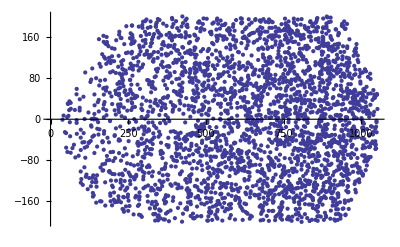

```mathematica
XYList=Table[Error[[i,5;;7;;2]],{i,1,m}];
ListPlot[XYList]
```

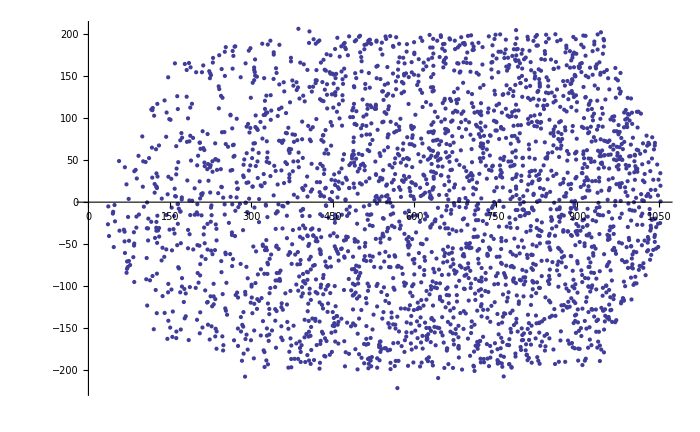

```mathematica
bestXYList=Table[Error[[i,9;;11;;2]],{i,1,m}];
ListPlot[bestXYList,ImageSize->700,PlotStyle-> PointSize[Small]]
```

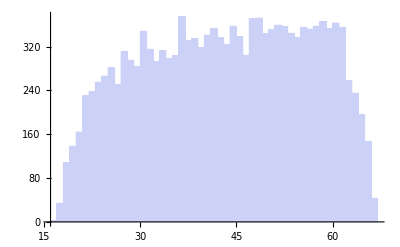

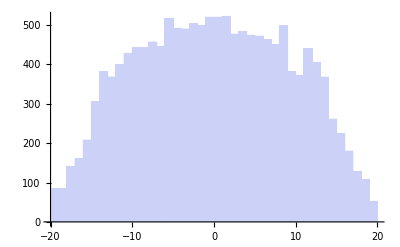

```mathematica
θList=Table[Error[[i,1]],{i,1,m}];
ϕList=Table[Error[[i,2]],{i,1,m}];
Histogram[θList,{1}]
Histogram[ϕList,{1}]
```

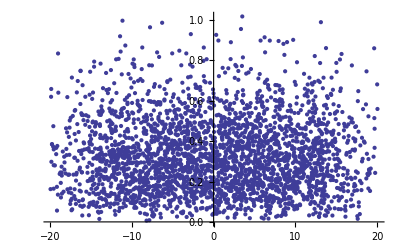

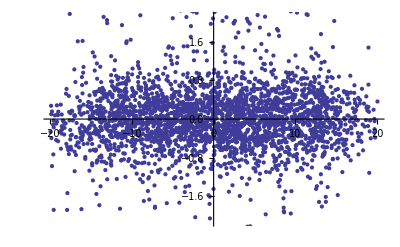

```mathematica
StatErrϕX=Table[Error[[i,4;;13;;9]],{i,1,m}];
SysErrϕX=Table[Error[[i,4;;17;;13]],{i,1,m}];
ListPlot[StatErrϕX]
ListPlot[SysErrϕX]
```

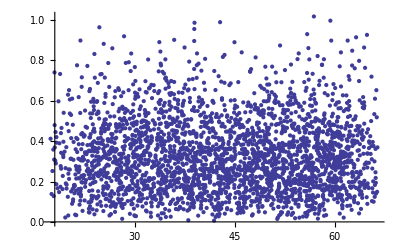

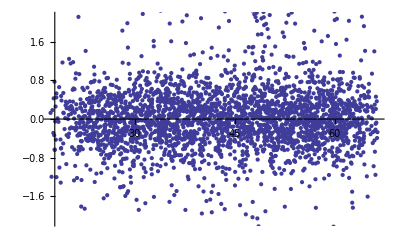

```mathematica
StatErrθX=Table[Error[[i,3;;13;;10]],{i,1,m}];
SysErrθX=Table[Error[[i,3;;17;;14]],{i,1,m}];
ListPlot[StatErrθX]
ListPlot[SysErrθX]
```

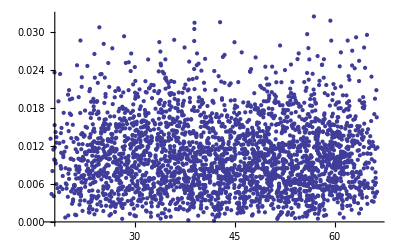

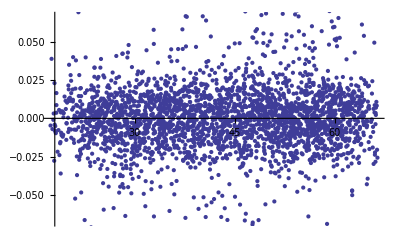

```mathematica
StatErrθA=Table[Error[[i,3;;14;;11]],{i,1,m}];
SysErrθA=Table[Error[[i,3;;18;;15]],{i,1,m}];
ListPlot[StatErrθA]
ListPlot[SysErrθA]
```

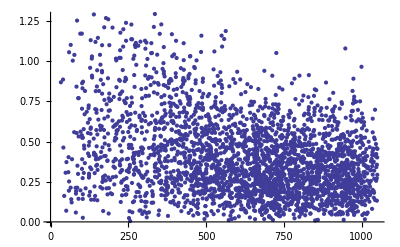

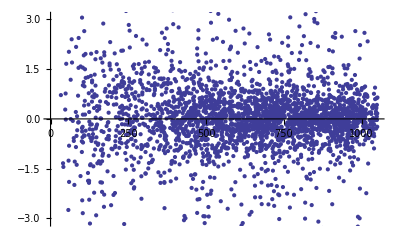

```mathematica
StatErrXX=Table[Error[[i,9;;13;;4]],{i,1,m}];
SysErrXX=Table[Error[[i,9;;17;;8]],{i,1,m}];
ListPlot[StatErrXX(*, PlotRange->{{500, 700},{0,1}}*)]
ListPlot[SysErrXX(*, PlotRange->{{500, 700},{-1,1}}*)]
```

```mathematica
Xerror=Table[Error[[i,13;;17;;4]],{i,1,m}];
ListPlot[Xerror]
```

```mathematica
errAA=Table[Error[[i,10;;14;;4]],{i,1,m}];
ListPlot[errAA]
```

```mathematica
PriXA=Table[Rayk[1,θ,0][[1;;2;;1]],{θ,15,70,1}];
PriXA1=Table[Rayk[1,θ,20][[1;;2;;1]],{θ,15,70,1}];
```

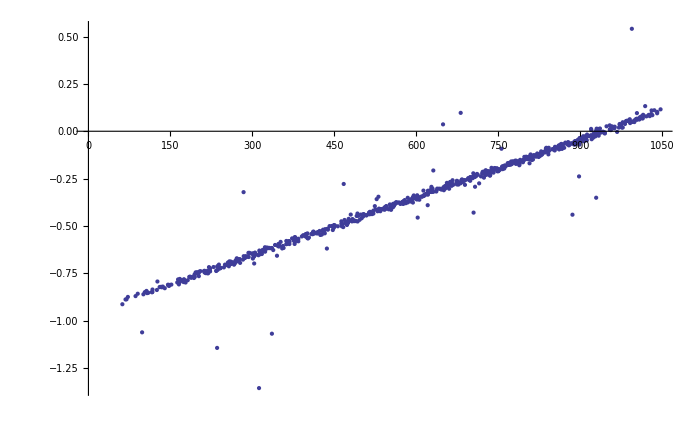

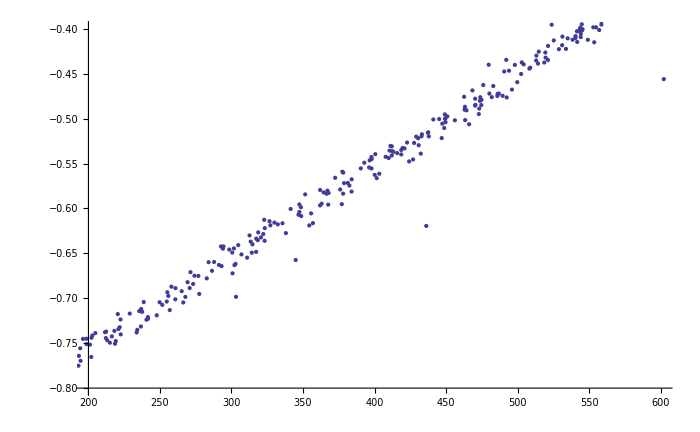

```mathematica
bestXA=Table[Error[[i,9;;10]],{i,1,m}];
ListPlot[bestXA,ImageSize->700,PlotStyle-> PointSize[Small]]
ListPlot[bestXA,PlotRange->{{200,600},{-0.8,-0.4}},PlotStyle-> PointSize[Small]]
```

```mathematica
(* Select |Y|<50 *)
YgatedError=Select[Error[[1;;m]],Abs[#[[11]]]>50&];
```

```mathematica
YgatedError[[1]]
```

```mathematica
mYg=Length[YgatedError]
```

26544

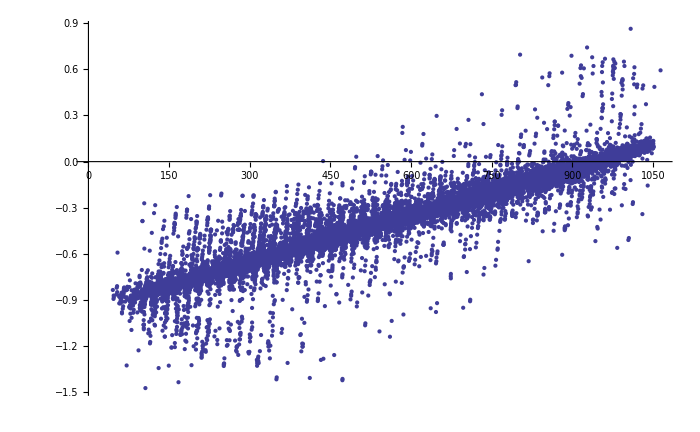

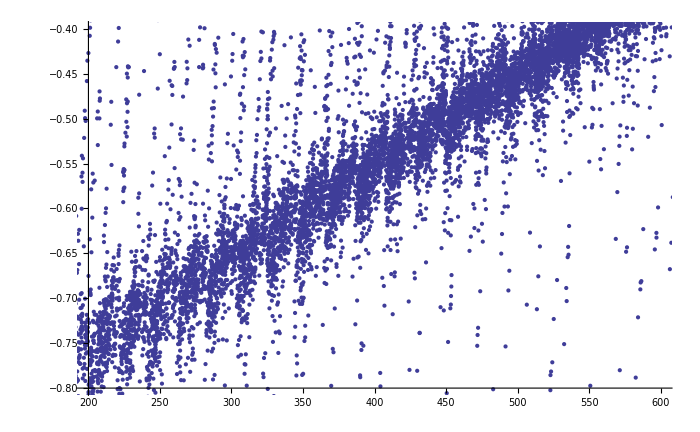

```mathematica
YgbestXA=Table[YgatedError[[i,9;;10]],{i,1,mYg}];
ListPlot[YgbestXA,ImageSize->700,PlotStyle-> PointSize[Small]]
ListPlot[YgbestXA,PlotRange->{{200,600},{-0.8,-0.4}},PlotStyle-> PointSize[Small]]
```

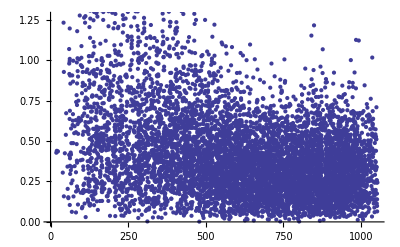

```mathematica
ListPlot[StatErrXX]
```

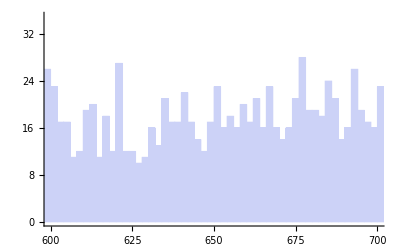

```mathematica
Histogram[TError[[9]],{2},PlotRange-> {{600,700},All}]
```

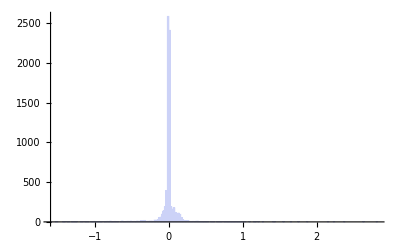

```mathematica
Histogram[TError[[20]]]
```

## Some Plots

```mathematica
(* Rayk at the end of the cell in X1 *)
MidkX1X2[mwdc_,wire_]:=Rayk[mwdc,LabAngleShift[mwdc]+(-1)^(mwdc+1)ArcCos[Normalize[(-(wstart[1,wire]+{10,0,0})+Crystal[mwdc])].{1,0,0}]*180/π,0]
(* Drift lenght of X1 and X2 *)
DriftX1X2[mwdc_,wire_]:={Abs[DriftLen[MidkX1X2[mwdc,wire],1,wire][[3]]],Abs[DriftLen[MidkX1X2[mwdc,wire],2,wire][[3]]]}

X1X2cell[mwdc_,cell_,shiftAngle_,id1_,id2_]:=MWDC2RaysFlat[
Rayk[mwdc,LabAngle[mwdc,1,cell][[id1]]-shiftAngle,0],Rayk[mwdc,LabAngle[mwdc,2,cell][[id2]],0],500,0.2,1]
X1X2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,If[mwdc==1,2,1],wire][[If[mwdc==1,1,3]]],LabAngle[mwdc,If[mwdc==1,1,2],wire][[If[mwdc==1,3,1]]],0.02}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1X1p[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire][[3]]]],DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]]},{i,LabAngle[mwdc,1,wire+1][[1]],LabAngle[mwdc,1,wire][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
X1pX2[mwdc_,wire_,color_]:=ListPlot[
Table[
k=Rayk[mwdc,i,0];
{DriftTime[Abs[DriftLen[k,1,wire+1][[3]]]],DriftTime[Abs[DriftLen[k,2,wire][[3]]]]},{i,LabAngle[mwdc,1,If[mwdc==1,wire,wire+1]][[1]],LabAngle[mwdc,2,If[mwdc==1,wire+1,wire]][[3]],0.01}]
,Joined->True,PlotRange->{{0,10.7},{0,10.7}},AspectRatio->1,PlotStyle->color]
(* the X2 Drift Len when X1 hit wire *)
AutoX1X2[mwdc_,cell_]:=DriftLen[Rayk[mwdc,LabAngle[mwdc,1,cell][[2]],0],2,cell][[3]]
AutoX1X2m[mwdc_,cell_]:=DriftLen[Rayk[mwdc,LabAngle[mwdc,1,cell][[2]],0],2,cell-1][[3]]
```

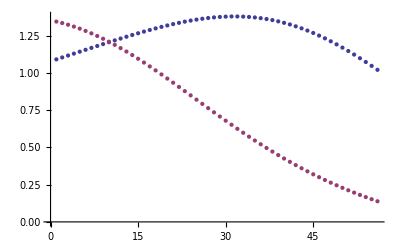

```mathematica
ListPlot[{
Table[LabAngle[1,1,i][[3]]-LabAngle[1,1,i][[1]],{i,56}],
Table[LabAngle[2,1,i][[1]]-LabAngle[2,1,i][[3]],{i,56}]}]
```

```mathematica
FindRoot[LabAngle[1,1,n][[2]]==10,{n,10}]
```

{n→-8.27879}

```mathematica
60-LabAngle[1,1,56][[2]]
```

-9.42277

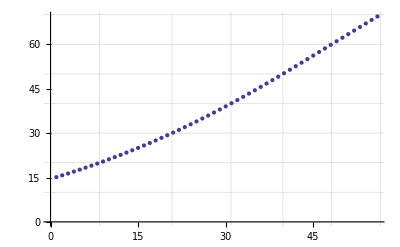

```mathematica
ListPlot[{
Table[{n,LabAngle[1,1,n][[2]]},{n,1,56}]
},GridLines->{{8.417,20.8092,30.9114,39.7951,48.143,56.4909},Table[10 i,{i,0,7}]}]
```

```mathematica
FindRoot[LabAngle[2,1,n][[2]]==70,{n,10}]
```

{n→1.65206}

```mathematica
60-LabAngle[2,1,56][[2]]
```

44.1754

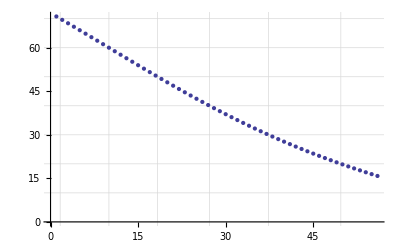

```mathematica
ListPlot[{
Table[{n,LabAngle[2,1,n][[2]]},{n,1,56}]
},GridLines->{{1.65206,10,18.3479,27.2316,37.338,49.7259},Table[10 i,{i,0,7}]}]
```

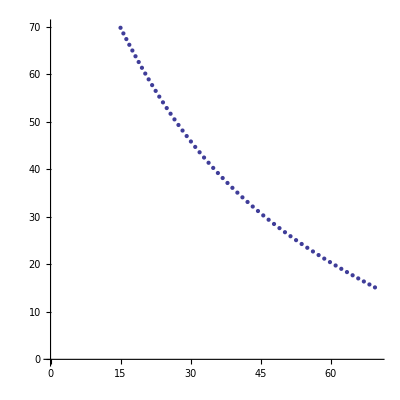

```mathematica
ListPlot[
Table[{LabAngle[1,1,n][[2]],LabAngle[2,1,n][[2]]},{n,1,56}]
,AspectRatio->1,PlotRange->{{0,70},{0,70}}]
```

### L - MWDC

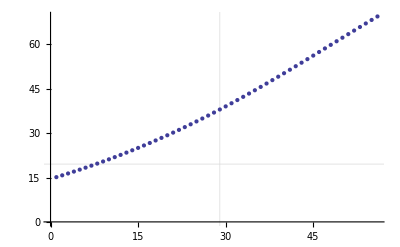

```mathematica
(* incident angle *)
ListPlot[Table[LabAngle[1,1,n][[2]],{n,1,56}],GridLines->{{29},{19.54}}]
```

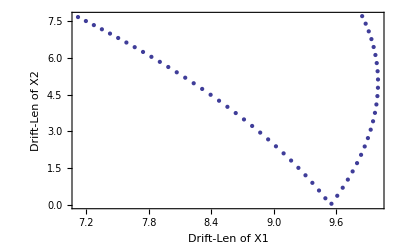

```mathematica
ListPlot[Table[DriftX1X2[1,i],{i,1,56}],Frame->True,FrameLabel->{"Drift-Len of X1","Drift-Len of X2"}]
```

```mathematica
X1X2cell[1,43,0,2,2]
X1X2cell[1,55,0,2,2]
```

-Graphics-

-Graphics-

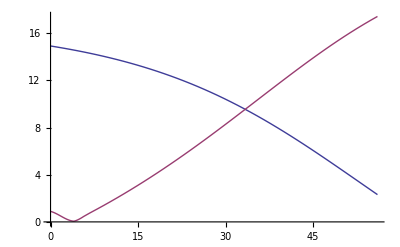

```mathematica
yintL=Table[{n,AutoX1X2[1,n]},{n,0,56,2}];
yintLm=Table[{n,AutoX1X2m[1,n]},{n,0,56,2}];
YintL=Interpolation[Abs[yintL]];
YintLm=Interpolation[Abs[yintLm]];
Plot[{YintL[x],YintLm[x]},{x,0,56},GridLines->{{18.02781807},{√(8^2+10^2)}}]
```

```mathematica
(* experiment data *)
expdataL={
{36,40+130},
{40,20+130},
{45,-10+130},
{47,-25+130},
{50,-50+130}};
expdataLint=Interpolation[expdataL];
```

```mathematica
FindRoot[YintL[x]-YintL[40]/expdataLint[40],{x,20,40}]
```

InterpolatingFunction::dmval: Input value {71.3989} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {63.5004} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{x→62.7919}

```mathematica
YintL[40]/expdataLint[40]
```

0.0509319

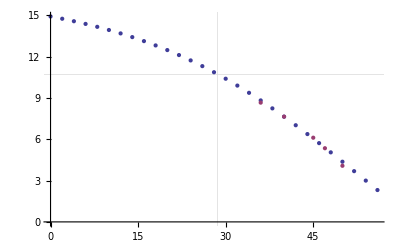

```mathematica
ListPlot[{Abs[yintL],Table[{expdataL[[i,1]],YintL[40]/expdataLint[40] expdataL[[i,2]]},{i,1,5}]},Joined->False, GridLines->{{28.6},{10.7}}]
```

### Plot

```mathematica
LabAngle[1,1,33][[2]]
60-LabAngle[1,1,33][[2]]
X1X2cell[1,33,0,2,2]
```

42.2629

17.7371

-Graphics-

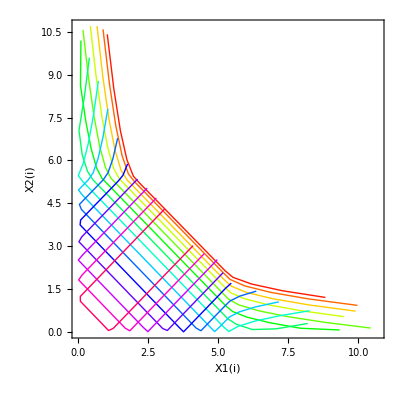

```mathematica
Show[Table[X1X2[1,i,Hue[i/60]],{i,{1, 4,8,12,16,20,24,28,32,36,40,44,48,52,56}}],Frame->True,FrameLabel->{"X1(i)","X2(i)"}]
```

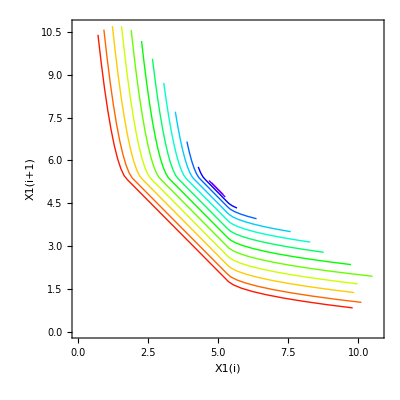

```mathematica
Show[Table[X1X1p[1,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X1(i+1)"}]
```

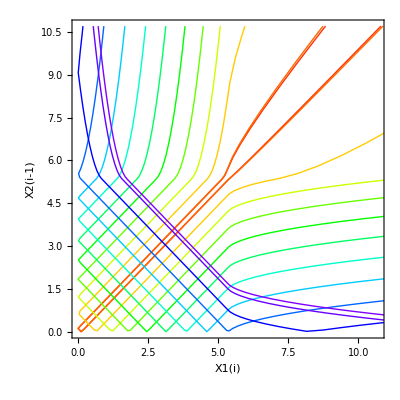

```mathematica
Show[Table[X1pX2[1,i,Hue[i/60]],{i,{2,4,8,12,16,20,24,28,32,36,40,44,45}}],Frame->True,FrameLabel->{"X1(i)","X2(i-1)"}]
```

### MWDC - R

```mathematica
LabAngle[2,1,10][[2]]
60-LabAngle[2,1,10][[2]]
X1X2cell[2,10,0,2,2]
```

60.

0.

-Graphics-

```mathematica
yintR=Table[{n,RAutoX1X2[n]},{n,1,56,1}];
```

```mathematica
Sort[Abs[yintR],#1[[2]]>#2[[2]]&][[-1]]
```

{25,0.0660956}

```mathematica
yintRdata=Map[#-{0,-130}&,{
{5,0},
{8,-25},
{12,-50},
{15,-60},
{20,-105},
{22,-110},
{28,-110},
{31,-90},
{32,-82},
{37,-60},
{39,-45},
{43,-30},
{47,-20},
{49,-10},
{52,0},
{56,20}}];
```

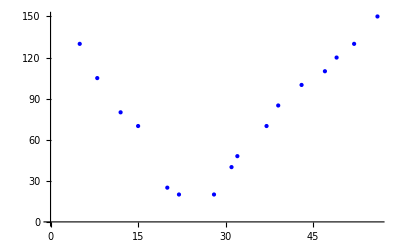

```mathematica
ListPlot[yintRdata,PlotStyle->{ Blue}]
```

```mathematica
yintR[[43,2]]/yintRdata[[12,2]]
```

0.0504738

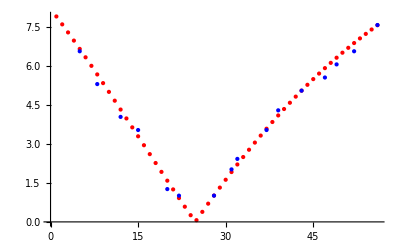

```mathematica
ListPlot[{Abs[yintR],Map[#*{1,yintR[[43,2]]/yintRdata[[12,2]]}&,yintRdata]},PlotStyle->{Red, Blue}]
```

### Plot

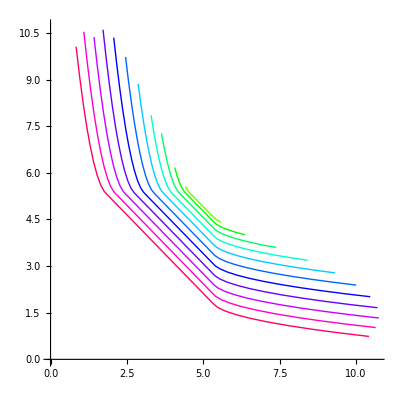

```mathematica
Show[Table[X1X1p[2,i,Hue[i/60]],{i,{16,20,24,28,32,36,40,44,48,52,56}}]]
```

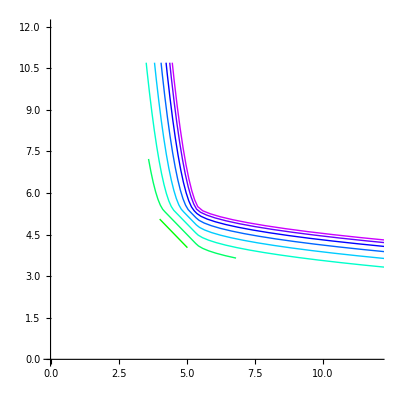

```mathematica
Show[Table[X1pX2[2,i,Hue[i/60]],{i,{20,24,28,32,36,40,44,48}}],PlotRange->{{0,12},{0,12}}]
```

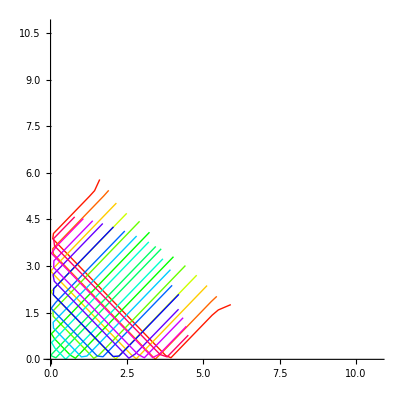

```mathematica
Show[Table[X1X2[2,i,Hue[i/60]],{i,{1,4,8,12,16,20,24,28,32,36,40,44,48,52,56}}]]
```

## PP elastics

```mathematica
mp=938.27203;
T1[T_,α_ ]:=T Cos[α °/2]^2
T2[T_,α_]:=T Sin[α °/2]^2
θ1[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Cos[α °/2]^2,(Sqrt[mp T] Sin[α °])/Sqrt[2]] 180/π
θ2[T_,α_(* deg *)](* deg *):=ArcTan[Sqrt[T (2 mp+T)] Sin[α °/2]^2,-((Sqrt[mp T] Sin[α °])/Sqrt[2])] 180/π
Einc[m_,ToF_ (*ns *),l_]:=With[{c=0.299792458},(m (c ToF √(c^2 ToF^2-l^2)-(c^2 ToF^2-l^2)))/(c^2 ToF^2-l^2)]
ToF[m_,Ein_,l_]:=With[{c=299792458},(l(m+Ein))/(c √(2m Ein+Ein^2))10^9](*ns*)
```

```mathematica
flL[α_]:=Norm[Ray[Rayk[1,θ1[260,α],0],200]-Crystal[1]] (* flight lenght *)
ToFTplL[α_]:=(flL[α](mp +T1[260,α]))/(299792458 √(2mp T1[260,α]+T1[260,α]^2))10^6 (* ns *)
flR[α_]:=Norm[Ray[Rayk[2,-θ2[260,α],0],200]-Crystal[2]] (* flight lenght *)
ToFTplR[α_]:=(flR[α](mp +T2[260,α]))/(299792458 √(2mp T2[260,α]+T2[260,α]^2))10^6 (* ns *)
```

```mathematica
(* Given Lab angle and find the ToF *)
FindRoot[θ1[260,α1]==70,{α1,50}]
ToFTplL[α1]/.%
```

{α1→142.33}

17.0867

```mathematica
(* Given ToF and find the lab angle *)
FindRoot[ToFTplL[α1]==8,{α1,100}]
θ1[260,α1]/.%
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{α1→67.7271}

32.1656

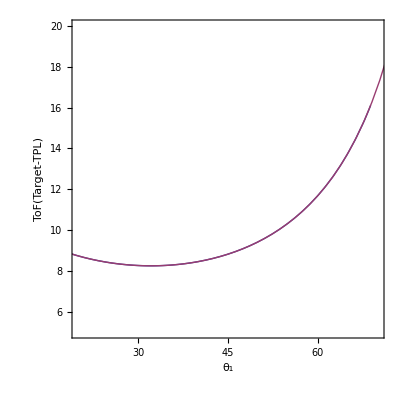

```mathematica
ParametricPlot[{{θ1[260,α],ToFTplL[α]},{-θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{20,70},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

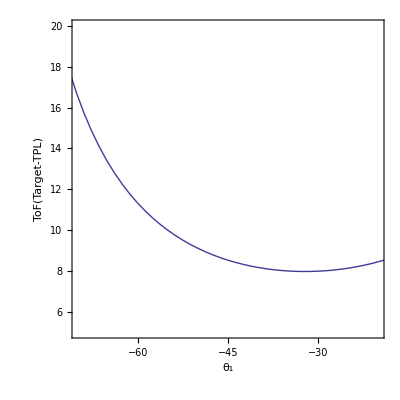

```mathematica
ParametricPlot[{{θ2[260,α],ToFTplR[α]}},{α,20,140},AspectRatio-> 1, PlotRange-> {{-70,-20},{5, 20}},Frame->True, FrameLabel-> {"θ_1","ToF(Target-TPL)"}]
```

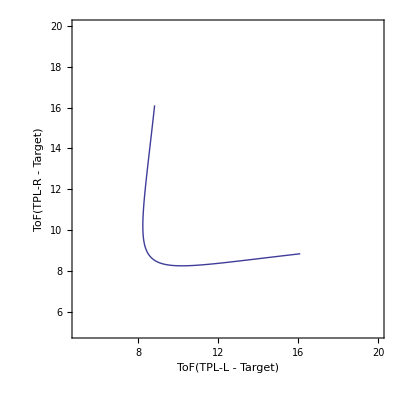

```mathematica
ParametricPlot[{ToFTplL[α],ToFTplR[α]},{α,40,140},AspectRatio-> 1, PlotRange-> {{5,20},{5, 20}},Frame->True, FrameLabel-> {"ToF(TPL-L - Target)","ToF(TPL-R - Target)"}]
```

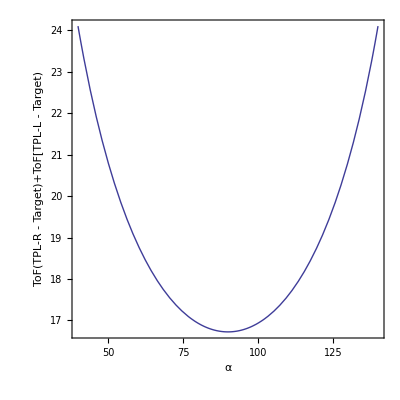

```mathematica
Plot[ToFTplL[α]+ToFTplR[α],{α,40,140},AspectRatio-> 1, Frame->True, FrameLabel-> {"α","ToF(TPL-R - Target)+ToF[TPL-L - Target)"}]
```

```mathematica
(* Timing of Plastics *)
```

```mathematica
F3[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i],{i,0,10}]
FH9[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-394.574],{i,0,10}]
Tgt[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844],{i,0,10}]
SO[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-463.046],{i,0,10}]
timingTpl=Table[ToFTplL[RandomReal[{42,142}]],{i,0,10}];
PLL[t_]:=Sum[Exp[-i/10]UnitBox[t-27 i-451.7844-timingTpl[[i+1]]],{i,0,10}]
```

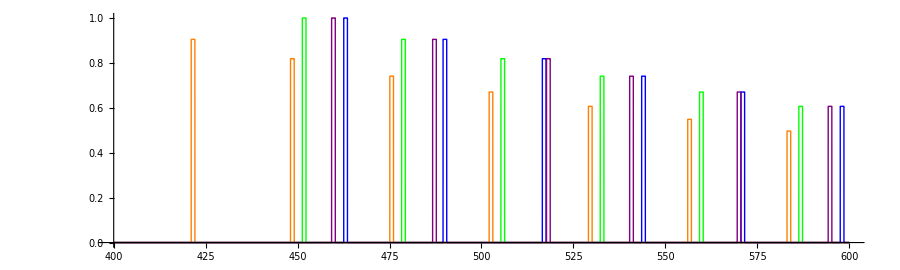

```mathematica
Plot[{F3[t],FH9[t],Tgt[t],SO[t],PLL[t]},{t,400,600},PlotPoints->400,AspectRatio->0.3,ImageSize->900,PlotStyle->{ Red,Orange, Green, Blue,Purple}]
```

```mathematica
θ1[260,90 ]
Rayk[1,θ1[260,90]]
HitList[Rayk[1,θ1[260,90]]][[1,2]]
```

43.1427

{655.949,0,631.708,0}

34

```mathematica
MWDC2RaysFlat[Rayk[1,θ1[260,90 ]],Rayk[1,θ1[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
MWDC2RaysFlat[Rayk[2,-θ2[260,90 ]],Rayk[2,-θ2[260,91 ]],500, 0.1,1]
```

-Graphics-

```mathematica
(* simulate MWDC L R ID *)
```

```mathematica
{HitList[Rayk[1,θ1[260,36]]][[1,2]],HitList[Rayk[2,-θ2[260,36]]][[1,2]]}
{HitList[Rayk[1,θ1[260,142]]][[1,2]],HitList[Rayk[2,-θ2[260,142]]][[1,2]]}
```

{4,1}

{56,53}

```mathematica
hist=Table[{HitList[Rayk[1,θ1[260,α]]][[1,2]],HitList[Rayk[2,-θ2[260,α]]][[1,2]]},{α,36,140,0.1}];
```

```mathematica
HistogramList[Transpose[hist][[1]],56]
```

{{4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.},{11,14,14,15,14,16,15,15,16,17,16,17,17,18,17,18,19,19,19,19,20,19,21,20,21,21,21,22,21,22,23,22,23,22,23,23,23,24,23,23,24,23,24,23,24,23,23,23,23,23,23,22}}

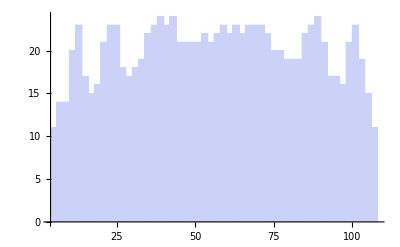

```mathematica
Histogram[Map[Total[#1]&,hist,{1}],56]
```

```mathematica
hist[[1]]
```

{4,1}

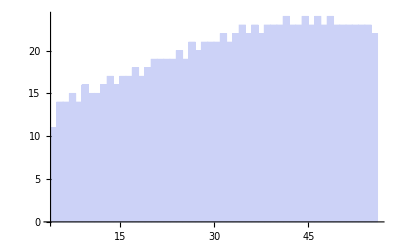

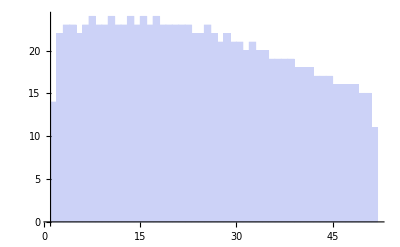

```mathematica
Histogram[Transpose[hist][[1]],56]
Histogram[Transpose[hist][[2]],56]
```

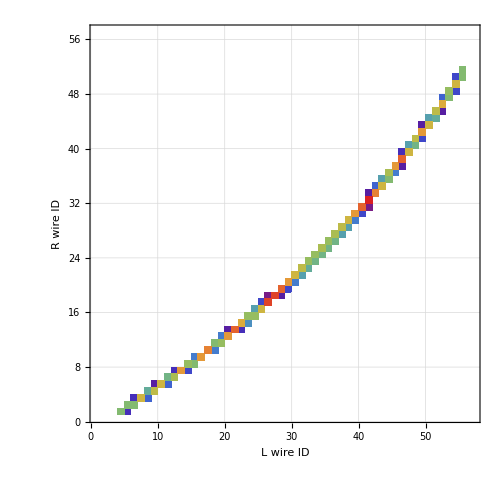

```mathematica
DensityHistogram[hist,56,GridLines->Automatic,PlotRange->{{1,57},{1,57}},ImageSize->500,Frame-> True,FrameLabel->{"L wire ID","R wire ID"},ColorFunction->"Rainbow"]
```

```mathematica
{Rayk[1,θ1[260,36]][[1]],Rayk[2,-θ2[260,36]][[1]]}
{Rayk[1,θ1[260,140]][[1]],Rayk[2,-θ2[260,140]][[1]]}
```

{57.9082,-1.97202}

{1089.03,1007.91}

```mathematica
histXLR=Table[{Rayk[1,θ1[260,α]][[1]],Rayk[2,-θ2[260,α]][[1]]},{α,36,140,0.1}];
```

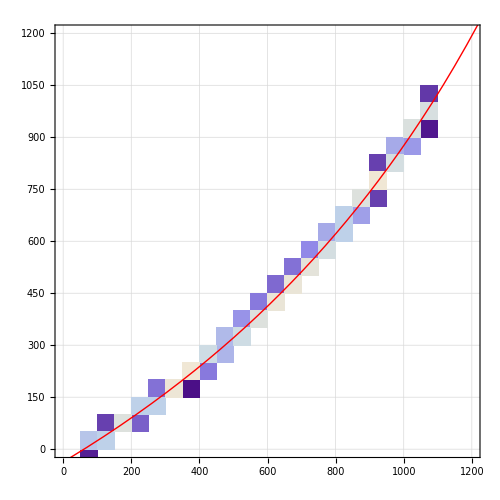

```mathematica
Show[DensityHistogram[histXLR,20,GridLines->Automatic,PlotRange->{{0,1200},{0,1200}},ImageSize->500],
ParametricPlot[{Rayk[1,θ1[260,α]][[1]],Rayk[2,-θ2[260,α]][[1]]},{α,0,180},PlotStyle->Red]]
```